# "Bad Romance" (2009)

## Lady Gaga

Arranged by Traci Johnson
Created July 7, 2010

```mathematica
-Graphics--Graphics--Graphics-
```

Ra^3+Ah^2+Roma(1+ma)+Ga^2+Oo+La^2+want+your+bad+romance^1

## Notes

So, I had to take a break from Mathematica in order to rescue my sanity, and for good reason because I have gone where no Mathematica songwriter has gone before^2! I have returned to give you the third installment of my series of Mathematica SoundNote[] creations inspired by Lady Gaga: Bad Romance. It's the longest of all the songs I've written: over a thousand lines of code^3 and close to five minutes in length!

Here are some answers to some frequently asked questions about these songs:
- I wrote all these songs by ear - listening to the tracks and plucking notes out on a virtual keyboard. Actually, this song compared to the first two had so many more instruments in it that I had to use YouTube to locate an audio track with instrumental parts only in order to hear everything in the background. So hopefully you'll appreciate my anal attention to detail when listening to this.
- I have absolutely no idea how I find the time to write these songs, but I usually only spend a couple hours at a time writing up the code. During the school year, I usually alternating my time writing with school work. Since its summer now, I've been spacing out Mathematica sessions with episodes of the X Files. By the time this notebook goes out on the internets, I will have watched all nine seasons (202 episodes) and both feature films in less than a six weeks^4.
- People miss this quite often, so I'll say it again. You can access the code by expanding the input bracket on the right side of the sound box thingy. I've got some mad commenting this time, including lyrics so if you're curious about instruments and such, all you have to do is follow the sound of Lady Gaga's vocals as you read them to yourself.

1: ...my Carleton password for the last three months (true fact!)
2: As far as I know!
3: Depending on how you define a line of code in this case. The last line reads 1157x+b. Quadruple digits, baby!
4: And wrote the theme song in Mathematica because I have no life!

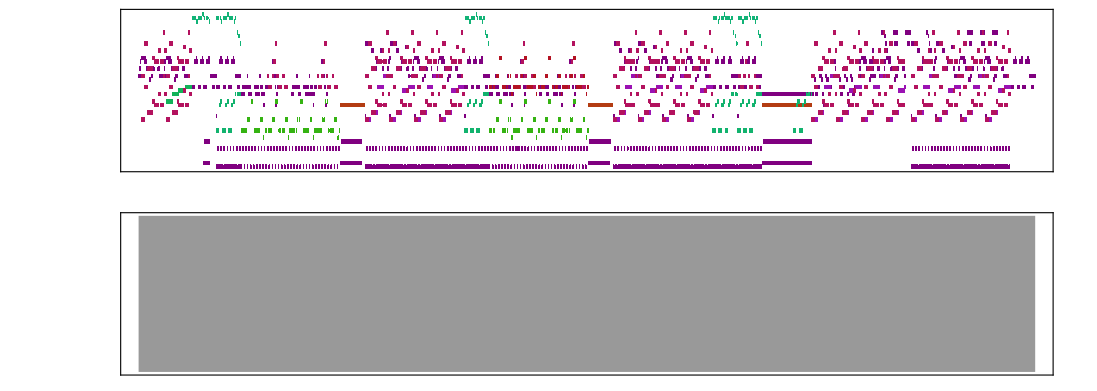

```mathematica
x=0.25;
b=3x;

Sound[{

(**************** Introduction ******************)

 (* whoa *)
SoundNote["C4",{-3x+b,-2x+b},"Piano"],
SoundNote["D4",{-2x+b,-1x+b},"Piano"],
SoundNote["E4",{-1x+b,0x+b},"Piano"],
SoundNote["C4",{0x+b,1 x+b},"Piano"],

SoundNote["F4",{1x+b,4 x+b},"Piano"],SoundNote[{"C3","C4"},{1x+b,5x+b},"Strings", SoundVolume->0.8],
SoundNote["E4",{4x+b,5x+b},"Piano"],
SoundNote["F4",{5x+b,6x+b},"Piano"],SoundNote[{"A3","A4"},{5x+b,9x+b},"Strings", SoundVolume->0.8],
SoundNote["E4",{6x+b,7 x+b},"Piano"],
SoundNote["D4",{7x+b,11x+b},"Piano"],SoundNote[{"D3","D4"},{9x+b,15x+b},"Strings", SoundVolume->0.8],
SoundNote["B3",{11x+b,13x+b},"Piano"],
SoundNote["C4" ,{13x+b,15x+b},"Piano"],
SoundNote["D4",{15x+b,17x+b},"Piano"],SoundNote[{"F3","F4"},{15x+b,17x+b},"Strings", SoundVolume->0.8],

(* caught in a bad romance *)
SoundNote["E4",{17x+b,18x+b},"Piano"],SoundNote[{"E3","E4"},{17x+b,23x+b},"Strings", SoundVolume->0.8],
SoundNote["E4",{18x+b,19x+b},"Piano"],
SoundNote["E4",{19x+b,20x+b},"Piano"],
SoundNote["E4",{20x+b,21x+b},"Piano"],
SoundNote["E4",{21x+b,22x+b},"Piano"],
SoundNote["D4",{22x+b,24x+b},"Piano"],SoundNote[{"G3","G4"},{23x+b,25x+b},"Strings", SoundVolume->0.8],
SoundNote["C4",{24x+b,29x+b},"Piano"],SoundNote[{"E3","E4"},{25x+b,29x+b},"Strings", SoundVolume->0.8],
SoundNote["C4",{29x+b,30x+b},"Piano"],
SoundNote["D4",{30x+b,31x+b},"Piano"],SoundNote[{"C4","C5"},{29x+b,31x+b},"Strings", SoundVolume->0.8],
SoundNote["E4",{31x+b,32x+b},"Piano"],
SoundNote["C4",{32x+b,33x+b},"Piano"],SoundNote[{"G3","G4"},{31x+b,33x+b},"Strings", SoundVolume->0.8],

(* whoa *)
SoundNote["F3",{33x+b, 34x+b},"Guitar"],SoundNote["F4",{33x+b,36 x+b},"Piano"],SoundNote[{"C3","C4"},{33x+b,37x+b},"Strings", SoundVolume->0.8],
SoundNote["F3",{34x+b, 35x+b},"Guitar"],
SoundNote["F3",{35x+b, 36x+b},"Guitar"],
SoundNote["F3",{36x+b, 37x+b},"Guitar"],SoundNote["E4",{36x+b,37x+b},"Piano"],
SoundNote["F3",{37x+b, 38x+b},"Guitar"],SoundNote["F4",{37x+b,38x+b},"Piano"],SoundNote[{"A3","A4"},{37x+b,41x+b},"Strings", SoundVolume->0.8],
SoundNote["F3",{38x+b, 39x+b},"Guitar"],SoundNote["E4",{38x+b,39x+b},"Piano"],
SoundNote["F3",{39x+b, 40x+b},"Guitar"],SoundNote["D4",{39x+b,43x+b},"Piano"],
SoundNote["F3",{40x+b, 41x+b},"Guitar"],
SoundNote["G3",{41x+b, 42x+b},"Guitar"],SoundNote[{"D3","D4"},{41x+b,47x+b},"Strings", SoundVolume->0.8],
SoundNote["G3",{42x+b, 43x+b},"Guitar"],
SoundNote["G3",{43x+b, 44x+b},"Guitar"],SoundNote["B3",{43x+b,45x+b},"Piano"],
SoundNote["G3",{44x+b, 45x+b},"Guitar"],
SoundNote["G3",{45x+b, 46x+b},"Guitar"],SoundNote["C4" ,{45x+b,47x+b},"Piano"],
SoundNote["G3",{46x+b, 47x+b},"Guitar"],
SoundNote["G3",{47x+b, 48x+b},"Guitar"],SoundNote["D4",{47x+b,49x+b},"Piano"],SoundNote[{"F3","F4"},{47x+b,49x+b},"Strings", SoundVolume->0.8],
SoundNote["G3",{48x+b, 49x+b},"Guitar"],

(* caught in a bad romance *)
SoundNote["G#3",{49x+b, 50x+b},"Guitar"],SoundNote["E4",{49x+b,50x+b},"Piano"],SoundNote[{"E3","E4"},{49x+b,55x+b},"Strings", SoundVolume->0.8],
SoundNote["G#3",{50x+b, 51x+b},"Guitar"],SoundNote["E4",{50x+b,51x+b},"Piano"],
SoundNote["G#3",{51x+b, 52x+b},"Guitar"],SoundNote["E4",{51x+b,52x+b},"Piano"],
SoundNote["G#3",{52x+b, 53x+b},"Guitar"],SoundNote["E4",{52x+b,53x+b},"Piano"],
SoundNote["G#3",{53x+b, 54x+b},"Guitar"],SoundNote["E4",{53x+b,54x+b},"Piano"],
SoundNote["G#3",{54x+b, 55x+b},"Guitar"],SoundNote["D4",{54x+b,56x+b},"Piano"],SoundNote[{"G#3","G#4"},{55x+b,57x+b},"Strings", SoundVolume->0.8],
SoundNote["G#3",{55x+b, 56x+b},"Guitar"],
SoundNote["G#3",{56x+b, 57x+b},"Guitar"],SoundNote["C4",{56x+b,61x+b},"Piano"],
SoundNote["A3",{57x+b, 58x+b},"Guitar"],SoundNote[{"E3","E4"},{57x+b,61x+b},"Strings", SoundVolume->0.8],
SoundNote["A3",{58x+b, 59x+b},"Guitar"],
SoundNote["A3",{59x+b, 60x+b},"Guitar"],
SoundNote["A3",{60x+b, 61x+b},"Guitar"],
SoundNote["A3",{61x+b, 62x+b},"Guitar"],SoundNote[{"C4","C5"},{61x+b,63x+b},"Strings", SoundVolume->0.8],
SoundNote["A3",{62x+b, 63x+b},"Guitar"],
SoundNote["A3",{63x+b, 64x+b},"Guitar"],SoundNote[{"G3","G4"},{63x+b,65x+b},"Strings", SoundVolume->0.8],
SoundNote["A3",{64x+b, 65x+b},"Guitar"], 


(*****************  Chant 1a, (acapella) *******************)

(* ra ra ra ah ah, ro ma, ro ma ma *)
SoundNote["A3",{65x+b, 67x+b},"Piano"],SoundNote["E5", {66x+b,66.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A3",{67x+b, 69x+b},"Piano"],SoundNote["E5", {68x+b,68.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E4",{69x+b, 70x+b},"Piano"],
SoundNote["E4",{70x+b, 71x+b},"Piano"],SoundNote["E5", {70x+b,70.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F4",{71x+b, 72x+b},"Piano"],
SoundNote["E4",{72x+b, 73x+b},"Piano"],SoundNote["D#5", {72x+b,72.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A3",{74x+b, 75x+b},"Piano"],SoundNote["E5", {74x+b,74.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A3",{75x+b, 77x+b},"Piano"],SoundNote["E5", {76x+b,76.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E4",{77x+b, 78x+b},"Piano"],
SoundNote["E4",{78x+b, 79x+b},"Piano"],SoundNote["E5", {78x+b,78.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F4",{79x+b, 80x+b},"Piano"],
SoundNote["E4",{80x+b, 81x+b},"Piano"],SoundNote["F5", {80x+b,80.5x+b},"PizzicatoStrings",SoundVolume->2],

(* Gaga oooo lala... want your bad romance *)
SoundNote["BassDrum2",{81x+b,82x+b}],SoundNote["A3",{81x+b, 83x+b},"Piano"],SoundNote["E5", {82x+b,82.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["HiHatClosed",{82x+b,83x+b}],
SoundNote["BassDrum2",{83x+b,84x+b}],SoundNote["A3",{83x+b, 85x+b},"Piano"],SoundNote["E5", {84x+b,84.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["HiHatClosed",{84x+b,85x+b}],
SoundNote["BassDrum2",{85x+b,86x+b}],SoundNote["E4",{85x+b, 86x+b},"Piano"],
SoundNote["HiHatClosed",{86x+b,87x+b}],SoundNote["E4",{86x+b, 87x+b},"Piano"],SoundNote["E5", {86x+b,86.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["BassDrum2",{87x+b,88x+b}],SoundNote["F4",{87x+b, 88x+b},"Piano"],
SoundNote["HiHatClosed",{88x+b,89x+b}],SoundNote["E4",{88x+b, 89x+b},"Piano"],SoundNote["D#5", {88x+b,88.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{90x+b, 91x+b},"Piano"],
SoundNote["C4",{91x+b, 92x+b},"Piano"],
SoundNote["A3",{92x+b, 93x+b},"Piano"],
SoundNote["C4",{93x+b, 94x+b},"Piano"],
SoundNote["A3",{94x+b, 95x+b},"Piano"],
SoundNote["C4",{95x+b, 97x+b},"Piano"],


(************* Chant 1b (start instrumental) **************)

(* ra ra ra ah ah, ro ma, ro ma ma *)
SoundNote["A2",{97x+b, 97.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{97x+b, 99x+b},"Piano"],SoundNote["BassDrum", {97x+b,98x+b}],SoundNote["CrashCymbal", {97x+b,98x+b}],
SoundNote["A2",{98x+b, 98.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {98x+b,98.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{99x+b, 99.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{99x+b, 101x+b},"Piano"],SoundNote["BassDrum", {99x+b,100x+b}],SoundNote["ElectricSnare", {99x+b,100x+b}],SoundNote["A2",{100x+b, 100.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {100x+b,100.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{101x+b, 101.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{101x+b, 102x+b},"Piano"],SoundNote["BassDrum", {101x+b,102x+b}],
SoundNote["E3",{102x+b, 102.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{102x+b, 103x+b},"Piano"],SoundNote["E5", {102x+b,102.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{103x+b, 103.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{103x+b, 104x+b},"Piano"],SoundNote["BassDrum", {103x+b,104x+b}],SoundNote["ElectricSnare", {103x+b,104x+b}],
SoundNote["F3",{104x+b, 104.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{104x+b, 105x+b},"Piano"],SoundNote["D#5", {104x+b,104.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{105x+b, 105.5x+b},"SynthBrass",SoundVolume->2],SoundNote["BassDrum", {105x+b,106x+b}],
SoundNote["A2",{106x+b, 106.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{106x+b, 107x+b},"Piano"],SoundNote["E5", {106x+b,106.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{107x+b, 107.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{107x+b, 109x+b},"Piano"],SoundNote["BassDrum", {107x+b,108x+b}],SoundNote["ElectricSnare", {107x+b,108x+b}],
SoundNote["A2",{108x+b, 108.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {108x+b,108.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{109x+b, 109.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{109x+b, 110x+b},"Piano"],SoundNote["BassDrum", {109x+b,110x+b}],
SoundNote["E3",{110x+b, 110.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{110x+b, 111x+b},"Piano"],SoundNote["E5", {110x+b,110.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{111x+b, 111.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{111x+b, 112x+b},"Piano"],SoundNote["BassDrum", {111x+b,112x+b}],SoundNote["ElectricSnare", {111x+b,112x+b}],
SoundNote["F3",{112x+b, 112.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{112x+b, 113x+b},"Piano"],SoundNote["F5", {112x+b,112.5x+b},"PizzicatoStrings",SoundVolume->2],

(* Gaga ooo lala... want your bad romance *)
SoundNote["A2",{113x+b, 113.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{113x+b, 115x+b},"Piano"],SoundNote["BassDrum", {113x+b,114x+b}],
SoundNote["A2",{114x+b, 114.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {114x+b,114.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{115x+b, 115.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{115x+b, 117x+b},"Piano"],SoundNote["BassDrum", {115x+b,116x+b}],SoundNote["ElectricSnare", {115x+b,116x+b}],
SoundNote["A2",{116x+b, 116.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {116x+b,116.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{117x+b, 117.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{117x+b, 118x+b},"Piano"],SoundNote["BassDrum", {117x+b,118x+b}],
SoundNote["E3",{118x+b, 118.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{118x+b, 119x+b},"Piano"],SoundNote["E5", {118x+b,118.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{119x+b, 119.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{119x+b, 120x+b},"Piano"],SoundNote["BassDrum", {119x+b,120x+b}],SoundNote["ElectricSnare", {119x+b,120x+b}],
SoundNote["F3",{120x+b, 120.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{120x+b, 121x+b},"Piano"],SoundNote["D#5", {120x+b,120.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["BassDrum", {121x+b,122x+b}],
SoundNote["G3",{122x+b, 122.5x+b},"SynthBrass",SoundVolume->2],SoundNote["C4",{122x+b, 123x+b},"Piano"],SoundNote["E5", {122x+b,122.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{123x+b, 124x+b},"Piano"],SoundNote["BassDrum", {123x+b,124x+b}],SoundNote["ElectricSnare", {123x+b,124x+b}],
SoundNote["G3",{124x+b, 124.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{124x+b, 125x+b},"Piano"],SoundNote["C5", {124x+b,124.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{125x+b, 126x+b},"Piano"],SoundNote["BassDrum", {125x+b,126x+b}],
SoundNote["G3",{126x+b, 126.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{126x+b, 127x+b},"Piano"],SoundNote["B4", {126x+b,126.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{127x+b, 129x+b},"Piano"],SoundNote["BassDrum", {127x+b,128x+b}],SoundNote["ElectricSnare", {127x+b,128x+b}],
SoundNote["G3",{128x+b, 128.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A4", {128x+b,128.5x+b},"PizzicatoStrings",SoundVolume->2],


(*********** Verse 1 ************)

(* I want your ugly, I want your disease *)
SoundNote["BassDrum",{129x+b,130x+b}],
SoundNote["A2",{130x+b, 130.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{130x+b, 131x+b},"Piano"],
SoundNote["ElectricSnare",{131x+b,132x+b}],SoundNote["A3",{131x+b, 132x+b},"Piano"],
SoundNote["A2",{132x+b, 132.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{132x+b, 133x+b},"Piano"],
SoundNote["BassDrum",{133x+b,134x+b}],SoundNote["A3",{133x+b, 134x+b},"Piano"],
SoundNote["A2",{134x+b, 134.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{134x+b, 135x+b},"Piano"],
SoundNote["ElectricSnare",{135x+b,136x+b}],
SoundNote["A2",{136x+b, 136.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{136x+b, 137x+b},"Piano"],
SoundNote["BassDrum",{137x+b,138x+b}],SoundNote["C4",{137x+b, 138x+b},"Piano"],
SoundNote["C3",{138x+b, 138.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{138x+b, 139x+b},"Piano"],
SoundNote["ElectricSnare",{139x+b,140x+b}],SoundNote["G3",{139x+b, 140x+b},"Piano"],
SoundNote["C3",{140x+b, 140.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{140x+b, 141x+b},"Piano"],
SoundNote["BassDrum",{141x+b,142x+b}],SoundNote["G3",{141x+b, 142x+b},"Piano"],
SoundNote["F3",{142x+b, 142.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{143x+b,144x+b}],
SoundNote["F3",{144x+b, 144.5x+b},"BaritoneSax",SoundVolume->2],

(* I want your everything as long as it's free... I want your love *)
SoundNote["BassDrum",{145x+b,146x+b}],
SoundNote["A2",{146x+b, 146.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{146x+b, 147x+b},"Piano"],
SoundNote["ElectricSnare",{147x+b,148x+b}],SoundNote["A3",{147x+b, 148x+b},"Piano"],
SoundNote["A2",{148x+b, 148.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{148x+b, 149x+b},"Piano"],
SoundNote["BassDrum",{149x+b,150x+b}],SoundNote["A3",{149x+b, 150x+b},"Piano"],
SoundNote["A2",{150x+b, 150.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{150x+b, 151x+b},"Piano"],
SoundNote["ElectricSnare",{151x+b,152x+b}],SoundNote["A3",{151x+b, 152x+b},"Piano"],
SoundNote["A2",{152x+b, 152.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{152x+b, 153x+b},"Piano"],
SoundNote["BassDrum",{153x+b,154x+b}],SoundNote["C4",{153x+b, 154x+b},"Piano"],
SoundNote["C3",{154x+b, 154.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{154x+b, 155x+b},"Piano"],
SoundNote["ElectricSnare",{155x+b,156x+b}],SoundNote["G3",{155x+b, 156x+b},"Piano"],
SoundNote["C3",{156x+b, 156.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{156x+b, 157x+b},"Piano"],
SoundNote["BassDrum",{157x+b,158x+b}],SoundNote["G3",{157x+b, 158x+b},"Piano"],
SoundNote["G2",{158x+b, 158.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["E3",{158x+b, 159x+b},"Piano"],
SoundNote["ElectricSnare",{159x+b,160x+b}],SoundNote["G3",{159x+b, 160x+b},"Piano"],
SoundNote["A2",{160x+b, 160.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{160x+b, 161x+b},"Piano"],


(* Love, love, love... I want your love *)
SoundNote["BassDrum",{161x+b,162x+b}],SoundNote["A3",{161x+b, 163x+b},"Piano"],
SoundNote["A2",{162x+b, 162.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{163x+b,164x+b}],SoundNote["C4",{163x+b,165x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{164x+b, 164.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{165x+b,166x+b}],SoundNote["A3",{165x+b,169x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{166x+b, 166.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{167x+b,168x+b}],
SoundNote["A2",{168x+b, 168.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{169x+b,170x+b}],SoundNote["E4",{169x+b, 171x+b},"Piano"],SoundNote["C4",{169x+b,171x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{170x+b, 170.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{171x+b,172x+b}],SoundNote["C4",{171x+b, 173x+b},"Piano"],SoundNote["E4",{171x+b,173x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{172x+b, 172.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{173x+b,174x+b}],SoundNote["A3",{173x+b, 174x+b},"Piano"],SoundNote["A4",{173x+b,175x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{174x+b, 174.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["E3",{174x+b, 175x+b},"Piano"],
SoundNote["ElectricSnare",{175x+b,176x+b}],SoundNote["G3",{175x+b, 176x+b},"Piano"],SoundNote["C4",{175x+b,177x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{176x+b, 176.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{176x+b, 177x+b},"Piano"],

SoundNote["BassDrum",{177x+b,178x+b}],SoundNote["A3",{177x+b, 179x+b},"Piano"],SoundNote["A3",{177x+b,181x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{178x+b, 178.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{179x+b,180x+b}],
SoundNote["A2",{180x+b, 180.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{181x+b,182x+b}],
SoundNote["A2",{182x+b, 182.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{183x+b,184x+b}],SoundNote["C4",{183x+b,185x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{184x+b, 184.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{185x+b,186x+b}],SoundNote["A3",{185x+b,189x+b},"Strings",SoundVolume->0.5],
SoundNote["C3",{186x+b, 186.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{187x+b,188x+b}],
SoundNote["C3",{188x+b, 188.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{189x+b,190x+b}],
SoundNote["G2",{190x+b, 190.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{191x+b,192x+b}],
SoundNote["A2",{192x+b, 192.5x+b},"BaritoneSax",SoundVolume->2],


(* I want your drama... the touch of your hand *)
SoundNote["BassDrum",{193x+b,194x+b}],
SoundNote["A2",{194x+b, 194.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{194x+b, 195x+b},"Piano"],
SoundNote["ElectricSnare",{195x+b,196x+b}],SoundNote["A3",{195x+b, 196x+b},"Piano"],
SoundNote["A2",{196x+b, 196.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{196x+b, 197x+b},"Piano"],
SoundNote["BassDrum",{197x+b,198x+b}],SoundNote["A3",{197x+b, 198x+b},"Piano"],
SoundNote["A2",{198x+b, 198.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{198x+b, 199x+b},"Piano"],
SoundNote["ElectricSnare",{199x+b,200x+b}],
SoundNote["A2",{200x+b, 200.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{200x+b, 201x+b},"Piano"],
SoundNote["BassDrum",{201x+b,202x+b}],SoundNote["C4",{201x+b, 202x+b},"Piano"],
SoundNote["C3",{202x+b, 202.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{202x+b, 203x+b},"Piano"],
SoundNote["ElectricSnare",{203x+b,204x+b}],SoundNote["G3",{203x+b, 204x+b},"Piano"],
SoundNote["C3",{204x+b, 204.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{204x+b, 205x+b},"Piano"],
SoundNote["BassDrum",{205x+b,206x+b}],SoundNote["G3",{205x+b, 206x+b},"Piano"],
SoundNote["F3",{206x+b, 206.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{207x+b,208x+b}],
SoundNote["F3",{208x+b, 208.5x+b},"BaritoneSax",SoundVolume->2],

(* I want your leather studded kiss in the sand *)
SoundNote["BassDrum",{209x+b,210x+b}],
SoundNote["A2",{210x+b, 210.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{210x+b, 211x+b},"Piano"],
SoundNote["ElectricSnare",{211x+b,212x+b}],SoundNote["A3",{211x+b, 212x+b},"Piano"],
SoundNote["A2",{212x+b, 212.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{212x+b, 213x+b},"Piano"],
SoundNote["BassDrum",{213x+b,214x+b}],SoundNote["A3",{213x+b, 214x+b},"Piano"],
SoundNote["A2",{214x+b, 214.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{214x+b, 215x+b},"Piano"],
SoundNote["ElectricSnare",{215x+b,216x+b}],SoundNote["A3",{215x+b, 216x+b},"Piano"],
SoundNote["A2",{216x+b, 216.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{216x+b, 217x+b},"Piano"],
SoundNote["BassDrum",{217x+b,218x+b}],SoundNote["C4",{217x+b, 218x+b},"Piano"],
SoundNote["C3",{218x+b, 218.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{218x+b, 219x+b},"Piano"],
SoundNote["ElectricSnare",{219x+b,220x+b}],SoundNote["G3",{219x+b, 220x+b},"Piano"],
SoundNote["C3",{220x+b, 220.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{220x+b, 221x+b},"Piano"],
SoundNote["BassDrum",{221x+b,222x+b}],SoundNote["G3",{221x+b, 222x+b},"Piano"],
SoundNote["G2",{222x+b, 222.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["E3",{222x+b, 223x+b},"Piano"],
SoundNote["ElectricSnare",{223x+b,224x+b}],SoundNote["G3",{223x+b, 224x+b},"Piano"],
SoundNote["A2",{224x+b, 224.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{224x+b, 225x+b},"Piano"],

(* Love, love, love... I want your love *)
SoundNote["BassDrum",{225x+b,226x+b}],SoundNote["A3",{225x+b, 227x+b},"Piano"],
SoundNote["A2",{226x+b, 226.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{227x+b,228x+b}],SoundNote["C4",{227x+b,229x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{228x+b, 228.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{229x+b,230x+b}],SoundNote["A3",{229x+b,233x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{230x+b, 230.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{231x+b,232x+b}],
SoundNote["A2",{232x+b, 232.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{233x+b,234x+b}],SoundNote["E4",{233x+b, 235x+b},"Piano"],SoundNote["C4",{233x+b,235x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{234x+b, 234.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{235x+b,236x+b}],SoundNote["C4",{235x+b, 237x+b},"Piano"],SoundNote["E4",{235x+b,237x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{236x+b, 236.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{237x+b,238x+b}],SoundNote["A3",{237x+b, 238x+b},"Piano"],SoundNote["A4",{237x+b,239x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{238x+b, 238.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["E3",{238x+b, 239x+b},"Piano"],
SoundNote["ElectricSnare",{239x+b,240x+b}],SoundNote["G3",{239x+b, 240x+b},"Piano"],SoundNote["C4",{239x+b,241x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{240x+b, 240.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{240x+b, 241x+b},"Piano"],

SoundNote["BassDrum",{241x+b,242x+b}],SoundNote["A3",{241x+b, 243x+b},"Piano"],SoundNote["A3",{241x+b,245x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{242x+b, 242.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{243x+b,244x+b}],
SoundNote["A2",{244x+b, 244.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{245x+b,246x+b}],
SoundNote["A2",{246x+b, 246.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{247x+b,248x+b}],SoundNote["C4",{247x+b,249x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{248x+b, 248.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{249x+b,250x+b}],SoundNote["A3",{249x+b,253x+b},"Strings",SoundVolume->0.5],
SoundNote["C3",{250x+b, 250.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{251x+b,252x+b}],
SoundNote["C3",{252x+b, 252.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["BassDrum",{253x+b,254x+b}],
SoundNote["G2",{254x+b, 254.5x+b},"BaritoneSax",SoundVolume->2],
SoundNote["ElectricSnare",{255x+b,256x+b}],
SoundNote["A2",{256x+b, 256.5x+b},"BaritoneSax",SoundVolume->2],


(***************** Pre-Chorus 1 *****************)

(* you know that I want you... and you know that I need you *)
SoundNote["E3",{257x+b, 257.5x+b},"FrenchHorn",SoundVolume->0.25],SoundNote["BassDrum2",{257x+b,258x+b}],
SoundNote["E3",{258x+b, 258.5x+b},"FrenchHorn",SoundVolume->0.30],SoundNote["HiHatClosed",{258x+b,259x+b}],
SoundNote["E3",{259x+b, 259.5x+b},"FrenchHorn",SoundVolume->0.35],SoundNote["BassDrum2",{259x+b,260x+b}],
SoundNote["E3",{260x+b, 260.5x+b},"FrenchHorn",SoundVolume->0.40],SoundNote["HiHatClosed",{260x+b,261x+b}],
SoundNote["E3",{261x+b, 261.5x+b},"FrenchHorn",SoundVolume->0.45],SoundNote["BassDrum2",{261x+b,262x+b}],
SoundNote["E3",{262x+b, 262.5x+b},"FrenchHorn",SoundVolume->0.50],SoundNote["HiHatClosed",{262x+b,263x+b}],
SoundNote["E3",{263x+b, 263.5x+b},"FrenchHorn",SoundVolume->0.55],SoundNote["BassDrum2",{263x+b,264x+b}],
SoundNote["E3",{264x+b, 264.5x+b},"FrenchHorn",SoundVolume->0.60],SoundNote["HiHatClosed",{264x+b,265x+b}],
SoundNote["E3",{265x+b, 265.5x+b},"FrenchHorn",SoundVolume->0.65],SoundNote["BassDrum2",{265x+b,266x+b}],
SoundNote["E3",{266x+b, 266.5x+b},"FrenchHorn",SoundVolume->0.70],SoundNote["HiHatClosed",{266x+b,267x+b}],
SoundNote["E3",{267x+b, 267.5x+b},"FrenchHorn",SoundVolume->0.75],SoundNote["BassDrum2",{267x+b,268x+b}],
SoundNote["E3",{268x+b, 268.5x+b},"FrenchHorn",SoundVolume->0.80],SoundNote["HiHatClosed",{268x+b,269x+b}],
SoundNote["E3",{269x+b, 269.5x+b},"FrenchHorn",SoundVolume->0.85],SoundNote["BassDrum2",{269x+b,270x+b}],
SoundNote["E3",{270x+b, 270.5x+b},"FrenchHorn",SoundVolume->0.90],SoundNote["HiHatClosed",{270x+b,271x+b}],
SoundNote["E3",{271x+b, 271.5x+b},"FrenchHorn",SoundVolume->0.95],SoundNote["BassDrum2",{271x+b,272x+b}],
SoundNote["E3",{272x+b, 272.5x+b},"FrenchHorn",SoundVolume->1.00],SoundNote["HiHatClosed",{272x+b,273x+b}],

(* I want it bad... bad romance *)
SoundNote["E3",{273x+b, 273.5x+b},"FrenchHorn",SoundVolume->1.05],SoundNote["BassDrum2",{273x+b,274x+b}],
SoundNote["E3",{274x+b, 274.5x+b},"FrenchHorn",SoundVolume->1.10],SoundNote["HiHatClosed",{274x+b,275x+b}],
SoundNote["E3",{275x+b, 275.5x+b},"FrenchHorn",SoundVolume->1.15],SoundNote["BassDrum2",{275x+b,276x+b}],
SoundNote["E3",{276x+b, 276.5x+b},"FrenchHorn",SoundVolume->1.20],SoundNote["HiHatClosed",{276x+b,277x+b}],
SoundNote["E3",{277x+b, 277.5x+b},"FrenchHorn",SoundVolume->1.25],SoundNote["BassDrum2",{277x+b,278x+b}],
SoundNote["E3",{278x+b, 278.5x+b},"FrenchHorn",SoundVolume->1.30],SoundNote["HiHatClosed",{278x+b,279x+b}],
SoundNote["E3",{279x+b, 279.5x+b},"FrenchHorn",SoundVolume->1.35],SoundNote["BassDrum2",{279x+b,280x+b}],
SoundNote["E3",{280x+b, 280.5x+b},"FrenchHorn",SoundVolume->1.40],SoundNote["HiHatClosed",{280x+b,281x+b}],
SoundNote["E3",{281x+b, 281.5x+b},"FrenchHorn",SoundVolume->1.45],SoundNote["BassDrum2",{281x+b,282x+b}],
SoundNote["E3",{282x+b, 282.5x+b},"FrenchHorn",SoundVolume->1.50],SoundNote["HiHatClosed",{282x+b,283x+b}],
SoundNote["E3",{283x+b, 283.5x+b},"FrenchHorn",SoundVolume->1.55],SoundNote["BassDrum2",{283x+b,284x+b}],
SoundNote["E3",{284x+b, 284.5x+b},"FrenchHorn",SoundVolume->1.60],SoundNote["HiHatClosed",{284x+b,285x+b}],
SoundNote["E3",{285x+b, 285.5x+b},"FrenchHorn",SoundVolume->1.65],
SoundNote["E3",{286x+b, 286.5x+b},"FrenchHorn",SoundVolume->1.70],
SoundNote["E3",{287x+b, 287.5x+b},"FrenchHorn",SoundVolume->1.75],
SoundNote["E3",{288x+b, 288.5x+b},"FrenchHorn",SoundVolume->1.80],

(************ Chorus 1 **********)

(* I want your love and I want your revenge *)
SoundNote["C3",{289x+b,289.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{289x+b,290x+b}],SoundNote[{"C3","C4"},{289x+b,293x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{289x+b,290x+b}],
SoundNote["C3",{290x+b,290.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{290x+b,291 x+b},"Piano"],
SoundNote["C3",{291x+b,291.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{291x+b,292 x+b},"Piano"],SoundNote["BassDrum",{291x+b,292x+b}],SoundNote["ElectricSnare",{291x+b,292x+b}],
SoundNote["C3",{292x+b,292.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{292x+b,293 x+b},"Piano"],
SoundNote["C3",{293x+b,293.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{293x+b,294 x+b},"Piano"],SoundNote["BassDrum",{293x+b,294x+b}],SoundNote[{"A3","A4"},{293x+b,297x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{294x+b,294.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{294x+b,295 x+b},"Piano"],
SoundNote["C3",{295x+b,295.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{295x+b,296x+b}],SoundNote["ElectricSnare",{295x+b,296x+b}],
SoundNote["C3",{296x+b,296.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{296x+b,297 x+b},"Piano"],
SoundNote["D3",{297x+b,297.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{297x+b,298x+b},"Piano"],SoundNote["BassDrum",{297x+b,298x+b}],SoundNote[{"D3","D4"},{297x+b,303x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{298x+b,298.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{298x+b,299x+b},"Piano"],
SoundNote["D3",{299x+b,299.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{299x+b,300x+b},"Piano"],SoundNote["BassDrum",{299x+b,300x+b}],SoundNote["ElectricSnare",{299x+b,300x+b}],
SoundNote["D3",{300x+b,300.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{300x+b,302x+b},"Piano"],
SoundNote["D3",{301x+b,301.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{301x+b,302x+b}],
SoundNote["D3",{302x+b,302.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{302x+b,303x+b},"Piano"],
SoundNote["D3",{303x+b,303.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{303x+b,304x+b},"Piano"],SoundNote["BassDrum",{303x+b,304x+b}],SoundNote["ElectricSnare",{303x+b,304x+b}],SoundNote[{"F3","F4"},{303x+b,305x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{304x+b,304.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{304x+b,305x+b},"Piano"],

(* you and me could write a bad romance *)
SoundNote["A3",{305x+b,305.5x+b},"Organ"],SoundNote["BassDrum",{305x+b,306x+b}],SoundNote[{"E3","E4"},{305x+b,311x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{306x+b,306.5x+b},"Organ"],SoundNote["E4",{306x+b,307 x+b},"Piano"],
SoundNote["A3",{307x+b,307.5x+b},"Organ"],SoundNote["E4",{307x+b,308 x+b},"Piano"],SoundNote["BassDrum",{307x+b,308x+b}],SoundNote["ElectricSnare",{307x+b,308x+b}],
SoundNote["A3",{308x+b,308.5x+b},"Organ"],SoundNote["E4",{308x+b,309 x+b},"Piano"],
SoundNote["A3",{309x+b,309.5x+b},"Organ"],SoundNote["G4",{309x+b,310 x+b},"Piano"],SoundNote["BassDrum",{309x+b,310x+b}],
SoundNote["A3",{310x+b,310.5x+b},"Organ"],
SoundNote["A3",{311x+b,311.5x+b},"Organ"],SoundNote["D4",{311x+b,312 x+b},"Piano"],SoundNote[{"G3","G4"},{311x+b,313x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{311x+b,312x+b}],SoundNote["ElectricSnare",{311x+b,312x+b}],
SoundNote["A3",{312x+b,312.5x+b},"Organ"],SoundNote["D4",{312x+b,313 x+b},"Piano"],
SoundNote["C4",{313x+b,313.5x+b},"Organ"],SoundNote["C4",{313x+b,315x+b},"Piano"],SoundNote["BassDrum",{313x+b,314x+b}],SoundNote[{"E3","E4"},{313x+b,317x+b},"Strings", SoundVolume->0.6],
SoundNote["C4",{314x+b,314.5x+b},"Organ"],
SoundNote["C4",{315x+b,315.5x+b},"Organ"],SoundNote["BassDrum",{315x+b,316x+b}],SoundNote["ElectricSnare",{315x+b,316x+b}],
SoundNote["C4",{316x+b,316.5x+b},"Organ"],
SoundNote["C4",{317x+b,317.5x+b},"Organ"],SoundNote["C4",{317x+b,318x+b},"Piano",SoundVolume->0.75],SoundNote[{"C4","C5"},{317x+b,319x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{317x+b,318x+b}],
SoundNote["C4",{318x+b,318.5x+b},"Organ"],SoundNote["D4",{318x+b,319 x+b},"Piano",SoundVolume->0.75],
SoundNote["C4",{319x+b,319.5x+b},"Organ"],SoundNote["E4",{319x+b,320 x+b},"Piano",SoundVolume->0.75],SoundNote[{"G3","G4"},{319x+b,321x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{319x+b,320x+b}],SoundNote["ElectricSnare",{319x+b,320x+b}],
SoundNote["C4",{320x+b,320.5x+b},"Organ"],SoundNote["C4",{320x+b,321 x+b},"Piano",SoundVolume->0.75],

(* I want your love and all your lover's revenge *)
SoundNote["C3",{321x+b,321.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{321x+b,322 x+b},"Piano",SoundVolume->0.75],SoundNote["BassDrum",{321x+b,322x+b}],SoundNote[{"C3","C4"},{321x+b,325x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{321x+b,322x+b}],
SoundNote["C3",{322x+b,322.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{322x+b,323 x+b},"Piano"],
SoundNote["C3",{323x+b,323.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{323x+b,324 x+b},"Piano"],SoundNote["BassDrum",{323x+b,324x+b}],SoundNote["ElectricSnare",{323x+b,324x+b}],
SoundNote["C3",{324x+b,324.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{324x+b,325 x+b},"Piano"],
SoundNote["C3",{325x+b,325.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{325x+b,326 x+b},"Piano"],SoundNote["BassDrum",{325x+b,326x+b}],SoundNote[{"A3","A4"},{325x+b,329x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{326x+b,326.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{326x+b,327 x+b},"Piano"],
SoundNote["C3",{327x+b,327.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{327x+b,328 x+b},"Piano"],SoundNote["BassDrum",{327x+b,328x+b}],SoundNote["ElectricSnare",{327x+b,328x+b}],
SoundNote["C3",{328x+b,328.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{328x+b,329 x+b},"Piano"],
SoundNote["D3",{329x+b,329.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{329x+b,330x+b},"Piano"],SoundNote["BassDrum",{329x+b,330x+b}],SoundNote[{"D3","D4"},{329x+b,335x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{330x+b,330.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{330x+b,331x+b},"Piano"],
SoundNote["D3",{331x+b,331.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{331x+b,332x+b},"Piano"],SoundNote["BassDrum",{331x+b,332x+b}],SoundNote["ElectricSnare",{331x+b,332x+b}],
SoundNote["D3",{332x+b,332.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{332x+b,334x+b},"Piano"],
SoundNote["D3",{333x+b,333.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{333x+b,334x+b}],
SoundNote["D3",{334x+b,334.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{334x+b,335x+b},"Piano"],
SoundNote["D3",{335x+b,335.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{335x+b,336x+b},"Piano"],SoundNote["BassDrum",{335x+b,336x+b}],SoundNote["ElectricSnare",{335x+b,336x+b}],SoundNote[{"F3","F4"},{335x+b,337x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{336x+b,336.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{336x+b,337x+b},"Piano"],

(* you and me could write a bad romance *)
SoundNote["G#3",{337x+b,337.5x+b},"Organ"],SoundNote["BassDrum",{337x+b,338x+b}],SoundNote[{"E3","E4"},{337x+b,343x+b},"Strings", SoundVolume->0.6],
SoundNote["G#3",{338x+b,338.5x+b},"Organ"],SoundNote["E4",{338x+b,339 x+b},"Piano"],
SoundNote["G#3",{339x+b,339.5x+b},"Organ"],SoundNote["E4",{339x+b,340 x+b},"Piano"],SoundNote["BassDrum",{339x+b,340x+b}],SoundNote["ElectricSnare",{339x+b,340x+b}],
SoundNote["G#3",{340x+b,340.5x+b},"Organ"],SoundNote["E4",{340x+b,341 x+b},"Piano"],
SoundNote["G#3",{341x+b,341.5x+b},"Organ"],SoundNote["G#4",{341x+b,342 x+b},"Piano"],SoundNote["BassDrum",{341x+b,342x+b}],
SoundNote["G#3",{342x+b,342.5x+b},"Organ"],
SoundNote["G#3",{343x+b,343.5x+b},"Organ"],SoundNote["D4",{343x+b,344 x+b},"Piano"],SoundNote[{"G#3","G#4"},{343x+b,345x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{343x+b,344x+b}],SoundNote["ElectricSnare",{343x+b,344x+b}],
SoundNote["G#3",{344x+b,344.5x+b},"Organ"],SoundNote["D4",{344x+b,345 x+b},"Piano"],
SoundNote["A3",{345x+b,345.5x+b},"Organ"],SoundNote["C4",{345x+b,347x+b},"Piano"],SoundNote["BassDrum",{345x+b,346x+b}],SoundNote[{"E3","E4"},{345x+b,349x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{346x+b,346.5x+b},"Organ"],
SoundNote["A3",{347x+b,347.5x+b},"Organ"],SoundNote["BassDrum",{347x+b,348x+b}],SoundNote["ElectricSnare",{347x+b,348x+b}],
SoundNote["A3",{348x+b,348.5x+b},"Organ"],
SoundNote["A3",{349x+b,349.5x+b},"Organ"],SoundNote["C4",{349x+b,350 x+b},"Piano"],SoundNote[{"C4","C5"},{349x+b,351x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{349x+b,350x+b}],
SoundNote["A3",{350x+b,350.5x+b},"Organ"],SoundNote["D4",{350x+b,351 x+b},"Piano"],
SoundNote["A3",{351x+b,351.5x+b},"Organ"],SoundNote["E4",{351x+b,352 x+b},"Piano"],SoundNote[{"G3","G4"},{351x+b,353x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{351x+b,352x+b}],SoundNote["ElectricSnare",{351x+b,352x+b}],
SoundNote["A3",{352x+b,352.5x+b},"Organ"],SoundNote["C4",{352x+b,353 x+b},"Piano"],


(*********** Post-Chorus 1 ****************)

(* whoa *)
SoundNote["C3",{353x+b,353.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{353x+b,356 x+b},"Piano"],SoundNote["BassDrum",{353x+b,354x+b}],SoundNote[{"C3","C4"},{353x+b,357x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{353x+b,354x+b}],
SoundNote["C3",{354x+b,354.5x+b},"Organ",SoundVolume->2],
SoundNote["C3",{355x+b,355.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{355x+b,356x+b}],SoundNote["ElectricSnare",{355x+b,356x+b}],
SoundNote["C3",{356x+b,356.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{356x+b,357x+b},"Piano"],
SoundNote["C3",{357x+b,357.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{357x+b,358x+b},"Piano"],SoundNote["BassDrum",{357x+b,358x+b}],SoundNote[{"A3","A4"},{357x+b,361x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{358x+b,358.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{358x+b,359x+b},"Piano"],
SoundNote["C3",{359x+b,359.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{359x+b,363x+b},"Piano"],SoundNote["BassDrum",{359x+b,360x+b}],SoundNote["ElectricSnare",{359x+b,360x+b}],
SoundNote["C3",{360x+b,360.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{361x+b,361.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{361x+b,362x+b}],SoundNote[{"D3","D4"},{361x+b,367x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{362x+b,362.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{363x+b,363.5x+b},"Organ",SoundVolume->2],SoundNote["B3",{363x+b,365x+b},"Piano"],SoundNote["BassDrum",{363x+b,364x+b}],SoundNote["ElectricSnare",{363x+b,364x+b}],
SoundNote["D3",{364x+b,364.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{365x+b,365.5x+b},"Organ",SoundVolume->2],SoundNote["C4",{365x+b,367x+b},"Piano"],SoundNote["BassDrum",{365x+b,366x+b}],
SoundNote["D3",{366x+b,366.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{367x+b,367.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{367x+b,369x+b},"Piano"],SoundNote["BassDrum",{367x+b,368x+b}],SoundNote["ElectricSnare",{367x+b,368x+b}],SoundNote[{"F3","F4"},{367x+b,369x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{368x+b,368.5x+b},"Organ",SoundVolume->2],

(* caught in a bad romance *)
SoundNote["A3",{369x+b,369.5x+b},"Organ"],SoundNote["E4",{369x+b,370x+b},"Piano"],SoundNote["BassDrum",{369x+b,370x+b}],SoundNote[{"E3","E4"},{369x+b,375x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{370x+b,370.5x+b},"Organ"],SoundNote["E4",{370x+b,371x+b},"Piano"],
SoundNote["A3",{371x+b,371.5x+b},"Organ"],SoundNote["E4",{371x+b,372x+b},"Piano"],SoundNote["BassDrum",{371x+b,372x+b}],SoundNote["ElectricSnare",{371x+b,372x+b}],
SoundNote["A3",{372x+b,372.5x+b},"Organ"],SoundNote["E4",{372x+b,373x+b},"Piano"],
SoundNote["A3",{373x+b,373.5x+b},"Organ"],SoundNote["E4",{373x+b,374x+b},"Piano"],SoundNote["BassDrum",{373x+b,374x+b}],
SoundNote["A3",{374x+b,374.5x+b},"Organ"],SoundNote["D4",{374x+b,375x+b},"Piano"],
SoundNote["A3",{375x+b,375.5x+b},"Organ"],SoundNote[{"G3","G4"},{375x+b,377x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{375x+b,376x+b}],SoundNote["ElectricSnare",{375x+b,376x+b}],
SoundNote["A3",{376x+b,376.5x+b},"Organ"],SoundNote["C4",{376x+b,381x+b},"Piano"],
SoundNote["C4",{377x+b,377.5x+b},"Organ"],SoundNote["BassDrum",{377x+b,378x+b}],SoundNote[{"E3","E4"},{377x+b,381x+b},"Strings", SoundVolume->0.6],
SoundNote["C4",{378x+b,378.5x+b},"Organ"],
SoundNote["C4",{379x+b,379.5x+b},"Organ"],SoundNote["BassDrum",{379x+b,380x+b}],SoundNote["ElectricSnare",{379x+b,380x+b}],
SoundNote["C4",{380x+b,380.5x+b},"Organ"],
SoundNote["C4",{381x+b,381.5x+b},"Organ"],SoundNote["C4",{381x+b,382x+b},"Piano"],SoundNote[{"C4","C5"},{381x+b,383x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{381x+b,382x+b}],
SoundNote["C4",{382x+b,382.5x+b},"Organ"],SoundNote["D4",{382x+b,383x+b},"Piano"],
SoundNote["C4",{383x+b,383.5x+b},"Organ"],SoundNote["E4",{383x+b,384x+b},"Piano"],SoundNote[{"G3","G4"},{383x+b,385x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{383x+b,384x+b}],SoundNote["ElectricSnare",{383x+b,384x+b}],
SoundNote["C4",{384x+b,384.5x+b},"Organ"],SoundNote["C4",{384x+b,385x+b},"Piano"],

(* whoa *)
SoundNote["C3",{385x+b,385.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{385x+b,388x+b},"Piano"],SoundNote["BassDrum",{385x+b,386x+b}],SoundNote[{"C3","C4"},{385x+b,389x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{385x+b,386x+b}],
SoundNote["C3",{386x+b,386.5x+b},"Organ",SoundVolume->2],
SoundNote["C3",{387x+b,387.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{387x+b,388x+b}],SoundNote["ElectricSnare",{387x+b,388x+b}],
SoundNote["C3",{388x+b,388.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{388x+b,389x+b},"Piano"],
SoundNote["C3",{389x+b,389.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{389x+b,390x+b},"Piano"],SoundNote["BassDrum",{389x+b,390x+b}],SoundNote[{"A3","A4"},{389x+b,393x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{390x+b,390.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{390x+b,391x+b},"Piano"],
SoundNote["C3",{391x+b,391.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{391x+b,395x+b},"Piano"],SoundNote["BassDrum",{391x+b,392x+b}],SoundNote["ElectricSnare",{391x+b,392x+b}],
SoundNote["C3",{392x+b,392.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{393x+b,393.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{393x+b,394x+b}],SoundNote[{"D3","D4"},{393x+b,399x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{394x+b,394.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{395x+b,395.5x+b},"Organ",SoundVolume->2],SoundNote["B3",{395x+b,397x+b},"Piano"],SoundNote["BassDrum",{395x+b,396x+b}],SoundNote["ElectricSnare",{395x+b,396x+b}],
SoundNote["D3",{396x+b,396.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{397x+b,397.5x+b},"Organ",SoundVolume->2],SoundNote["C4",{397x+b,399x+b},"Piano"],SoundNote["BassDrum",{397x+b,398x+b}],
SoundNote["D3",{398x+b,398.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{399x+b,399.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{399x+b,401x+b},"Piano"],SoundNote["BassDrum",{399x+b,400x+b}],SoundNote["ElectricSnare",{399x+b,400x+b}],SoundNote[{"F3","F4"},{399x+b,401x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{400x+b,400.5x+b},"Organ",SoundVolume->2],

(* caught in a bad romance *)
SoundNote["G#3",{401x+b,401.5x+b},"Organ"],SoundNote["E4",{401x+b,402x+b},"Piano"],SoundNote["BassDrum",{401x+b,402x+b}],SoundNote[{"E3","E4"},{401x+b,407x+b},"Strings", SoundVolume->0.6],
SoundNote["G#3",{402x+b,402.5x+b},"Organ"],SoundNote["E4",{402x+b,403x+b},"Piano"],
SoundNote["G#3",{403x+b,403.5x+b},"Organ"],SoundNote["E4",{403x+b,404x+b},"Piano"],SoundNote["BassDrum",{403x+b,404x+b}],SoundNote["ElectricSnare",{403x+b,404x+b}],
SoundNote["G#3",{404x+b,404.5x+b},"Organ"],SoundNote["E4",{404x+b,405x+b},"Piano"],
SoundNote["G#3",{405x+b,405.5x+b},"Organ"],SoundNote["E4",{405x+b,406x+b},"Piano"],SoundNote["BassDrum",{405x+b,406x+b}],
SoundNote["G#3",{406x+b,406.5x+b},"Organ"],SoundNote["D4",{406x+b,408x+b},"Piano"],
SoundNote["G#3",{407x+b,407.5x+b},"Organ"],SoundNote[{"G#3","G#4"},{407x+b,409x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{407x+b,408x+b}],SoundNote["ElectricSnare",{407x+b,408x+b}],
SoundNote["G#3",{408x+b,408.5x+b},"Organ"],SoundNote["C4",{408x+b,413x+b},"Piano"],
SoundNote["A3",{409x+b,409.5x+b},"Organ"],SoundNote["BassDrum",{409x+b,410x+b}],SoundNote[{"E3","E4"},{409x+b,413x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{410x+b,410.5x+b},"Organ"],
SoundNote["A3",{411x+b,411.5x+b},"Organ"],SoundNote["BassDrum",{411x+b,412x+b}],SoundNote["ElectricSnare",{411x+b,412x+b}],
SoundNote["A3",{412x+b,412.5x+b},"Organ"],
SoundNote["A3",{413x+b,413.5x+b},"Organ"],SoundNote[{"C4","C5"},{413x+b,415x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{413x+b,414x+b}],
SoundNote["A3",{414x+b,414.5x+b},"Organ"],
SoundNote["A3",{415x+b,415.5x+b},"Organ"],SoundNote[{"G3","G4"},{415x+b,417x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{415x+b,416x+b}],SoundNote["ElectricSnare",{415x+b,416x+b}],
SoundNote["A3",{416x+b,416.5x+b},"Organ"],


(**************** Chant 2 *****************)

(* ra ra ra ah ah, ro ma, ro ma ma *)
SoundNote["A2",{417x+b, 417.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{417x+b, 419x+b},"Piano"],SoundNote["BassDrum", {417x+b,418x+b}],SoundNote["CrashCymbal", {417x+b,418x+b}],
SoundNote["A2",{418x+b, 418.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {418x+b,418.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{419x+b, 419.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{419x+b, 421x+b},"Piano"],SoundNote["BassDrum", {419x+b,420x+b}],SoundNote["ElectricSnare", {419x+b,420x+b}],SoundNote["A2",{420x+b, 420.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {420x+b,420.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{421x+b, 421.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{421x+b, 422x+b},"Piano"],SoundNote["BassDrum", {421x+b,422x+b}],
SoundNote["E3",{422x+b, 422.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{422x+b, 423x+b},"Piano"],SoundNote["E5", {422x+b,422.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{423x+b, 423.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{423x+b, 424x+b},"Piano"],SoundNote["BassDrum", {423x+b,424x+b}],SoundNote["ElectricSnare", {423x+b,424x+b}],
SoundNote["F3",{424x+b, 424.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{424x+b, 425x+b},"Piano"],SoundNote["D#5", {424x+b,424.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{425x+b, 425.5x+b},"SynthBrass",SoundVolume->2],SoundNote["BassDrum", {425x+b,426x+b}],
SoundNote["A2",{426x+b, 426.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{426x+b, 427x+b},"Piano"],SoundNote["E5", {426x+b,426.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{427x+b, 427.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{427x+b, 429x+b},"Piano"],SoundNote["BassDrum", {427x+b,428x+b}],SoundNote["ElectricSnare", {427x+b,428x+b}],
SoundNote["A2",{428x+b, 428.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {428x+b,428.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{429x+b, 429.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{429x+b, 430x+b},"Piano"],SoundNote["BassDrum", {429x+b,430x+b}],
SoundNote["E3",{430x+b, 430.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{430x+b, 431x+b},"Piano"],SoundNote["E5", {430x+b,430.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{431x+b, 431.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{431x+b, 432x+b},"Piano"],SoundNote["BassDrum", {431x+b,432x+b}],SoundNote["ElectricSnare", {431x+b,432x+b}],
SoundNote["F3",{432x+b, 432.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{432x+b, 433x+b},"Piano"],SoundNote["F5", {432x+b,432.5x+b},"PizzicatoStrings",SoundVolume->2],

(* Gaga ooo lala... want your bad romance *)
SoundNote["A2",{433x+b, 433.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{433x+b, 435x+b},"Piano"],SoundNote["BassDrum", {433x+b,434x+b}],
SoundNote["A2",{434x+b, 434.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {434x+b,434.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{435x+b, 435.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{435x+b, 437x+b},"Piano"],SoundNote["BassDrum", {435x+b,436x+b}],SoundNote["ElectricSnare", {435x+b,436x+b}],
SoundNote["A2",{436x+b, 436.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {436x+b,436.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{437x+b, 437.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{437x+b, 438x+b},"Piano"],SoundNote["BassDrum", {437x+b,438x+b}],
SoundNote["E3",{438x+b, 438.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{438x+b, 439x+b},"Piano"],SoundNote["E5", {438x+b,438.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{439x+b, 439.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{439x+b, 440x+b},"Piano"],SoundNote["BassDrum", {439x+b,440x+b}],SoundNote["ElectricSnare", {439x+b,440x+b}],
SoundNote["F3",{440x+b, 440.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{440x+b, 441x+b},"Piano"],SoundNote["D#5", {440x+b,440.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["BassDrum", {441x+b,442x+b}],
SoundNote["G3",{442x+b, 442.5x+b},"SynthBrass",SoundVolume->2],SoundNote["C4",{442x+b, 443x+b},"Piano"],SoundNote["E5", {442x+b,442.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{443x+b, 444x+b},"Piano"],SoundNote["BassDrum", {443x+b,444x+b}],SoundNote["ElectricSnare", {443x+b,444x+b}],
SoundNote["G3",{444x+b, 444.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{444x+b, 445x+b},"Piano"],SoundNote["C5", {444x+b,444.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{445x+b, 446x+b},"Piano"],SoundNote["BassDrum", {445x+b,446x+b}],
SoundNote["G3",{446x+b, 446.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{446x+b, 447x+b},"Piano"],SoundNote["B4", {446x+b,446.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{447x+b, 449x+b},"Piano"],SoundNote["BassDrum", {447x+b,448x+b}],SoundNote["ElectricSnare", {447x+b,448x+b}],
SoundNote["G3",{448x+b, 448.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A4", {448x+b,448.5x+b},"PizzicatoStrings",SoundVolume->2],


(*********** Verse 2 ************)

(* I want your horror... I want your design *)
SoundNote["BassDrum",{449x+b,450x+b}],
SoundNote["A2",{450x+b, 450.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{450x+b,450.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{450x+b, 451x+b},"Piano"],
SoundNote["ElectricSnare",{451x+b,452x+b}],SoundNote["A3",{451x+b, 452x+b},"Piano"],
SoundNote["A2",{452x+b, 452.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{452x+b,452.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{452x+b, 453x+b},"Piano"],
SoundNote["BassDrum",{453x+b,454x+b}],SoundNote["A3",{453x+b, 454x+b},"Piano"],
SoundNote["A2",{454x+b, 454.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{454x+b,454.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{454x+b, 455x+b},"Piano"],
SoundNote["ElectricSnare",{455x+b,456x+b}],
SoundNote["A2",{456x+b, 456.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{456x+b,456.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{456x+b, 457x+b},"Piano"],
SoundNote["BassDrum",{457x+b,458x+b}],SoundNote["C4",{457x+b, 458x+b},"Piano"],
SoundNote["C3",{458x+b, 458.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{458x+b,458.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{458x+b, 459x+b},"Piano"],
SoundNote["ElectricSnare",{459x+b,460x+b}],SoundNote["G3",{459x+b, 460x+b},"Piano"],
SoundNote["C3",{460x+b, 460.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{460x+b,460.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{460x+b, 461x+b},"Piano"],
SoundNote["BassDrum",{461x+b,462x+b}],SoundNote["G3",{461x+b, 462x+b},"Piano"],
SoundNote["F3",{462x+b, 462.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{462x+b,462.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{463x+b,464x+b}],
SoundNote["F3",{464x+b, 464.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{464x+b,464.5x+b},"Polysynth",SoundVolume->0.7],

(* 'Cuz you're a criminal as long as you're mine... I want your love *)
SoundNote["BassDrum",{465x+b,466x+b}],
SoundNote["A2",{466x+b, 466.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{466x+b,466.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{466x+b, 467x+b},"Piano"],
SoundNote["ElectricSnare",{467x+b,468x+b}],SoundNote["A3",{467x+b, 468x+b},"Piano"],
SoundNote["A2",{468x+b, 468.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{468x+b,468.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{468x+b, 469x+b},"Piano"],
SoundNote["BassDrum",{469x+b,470x+b}],SoundNote["A3",{469x+b, 470x+b},"Piano"],
SoundNote["A2",{470x+b, 470.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{470x+b,470.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{470x+b, 471x+b},"Piano"],
SoundNote["ElectricSnare",{471x+b,472x+b}],SoundNote["A3",{471x+b, 472x+b},"Piano"],
SoundNote["A2",{472x+b, 472.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{472x+b,472.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{472x+b, 473x+b},"Piano"],
SoundNote["BassDrum",{473x+b,474x+b}],SoundNote["C4",{473x+b, 474x+b},"Piano"],
SoundNote["C3",{474x+b, 474.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{474x+b,474.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{474x+b, 475x+b},"Piano"],
SoundNote["ElectricSnare",{475x+b,476x+b}],SoundNote["G3",{475x+b, 476x+b},"Piano"],
SoundNote["C3",{476x+b, 476.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{476x+b,476.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{476x+b, 477x+b},"Piano"],
SoundNote["BassDrum",{477x+b,478x+b}],SoundNote["G3",{477x+b, 478x+b},"Piano"],
SoundNote["G2",{478x+b, 478.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{478x+b,478.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["E3",{478x+b, 479x+b},"Piano"],
SoundNote["ElectricSnare",{479x+b,480x+b}],SoundNote["G3",{479x+b, 480x+b},"Piano"],
SoundNote["A2",{480x+b, 480.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{480x+b,480.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{480x+b, 481x+b},"Piano"],

(* love, love, love... I want your love *)
SoundNote["BassDrum",{481x+b,482x+b}],SoundNote["A3",{481x+b, 483x+b},"Piano"],
SoundNote["A2",{482x+b, 482.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{482x+b,482.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{483x+b,485x+b}],SoundNote["C4",{483x+b,485x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{484x+b, 484.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{484x+b,484.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{485x+b,486x+b}],SoundNote["A3",{485x+b,489x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{486x+b, 486.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{486x+b,486.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{487x+b,488x+b}],
SoundNote["A2",{488x+b, 488.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{488x+b,488.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{489x+b,490x+b}],SoundNote["E4",{489x+b, 491x+b},"Piano"],SoundNote["C4",{489x+b,491x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{490x+b, 490.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{490x+b,490.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{491x+b,492x+b}],SoundNote["C4",{491x+b, 493x+b},"Piano"],SoundNote["E4",{491x+b,493x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{492x+b, 492.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{492x+b,492.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{493x+b,494x+b}],SoundNote["A3",{493x+b, 494x+b},"Piano"],SoundNote["A4",{493x+b,495x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{494x+b, 494.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{494x+b,494.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["E3",{494x+b, 495x+b},"Piano"],
SoundNote["ElectricSnare",{495x+b,496x+b}],SoundNote["G3",{495x+b, 496x+b},"Piano"],SoundNote["C4",{495x+b,497x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{496x+b, 496.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{496x+b,496.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{496x+b, 497x+b},"Piano"],

SoundNote["BassDrum",{497x+b,498x+b}],SoundNote["A3",{497x+b, 499x+b},"Piano"],SoundNote["A3",{497x+b,501x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{498x+b, 498.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{498x+b,498.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{499x+b,500x+b}],
SoundNote["A2",{500x+b, 500.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{500x+b,500.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{501x+b,502x+b}],
SoundNote["A2",{502x+b, 502.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{502x+b,502.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{503x+b,504x+b}],SoundNote["C4",{503x+b,505x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{504x+b, 504.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{504x+b,504.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{505x+b,506x+b}],SoundNote["A3",{505x+b,509x+b},"Strings",SoundVolume->0.5],
SoundNote["C3",{506x+b, 506.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{506x+b,506.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{507x+b,508x+b}],
SoundNote["C3",{508x+b, 508.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{508x+b,508.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{509x+b,510x+b}],
SoundNote["G2",{510x+b, 510.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{510x+b,510.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{511x+b,512x+b}],
SoundNote["A2",{512x+b, 512.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{512x+b,512.5x+b},"Polysynth",SoundVolume->0.7],

(* I want your psycho... your vertigo shtick *)
SoundNote["BassDrum",{513x+b,514x+b}],
SoundNote["A2",{514x+b, 514.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{514x+b,514.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{514x+b, 515x+b},"Piano"],
SoundNote["ElectricSnare",{515x+b,516x+b}],SoundNote["A3",{515x+b, 516x+b},"Piano"],
SoundNote["A2",{516x+b, 516.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{516x+b,516.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{516x+b, 517x+b},"Piano"],
SoundNote["BassDrum",{517x+b,518x+b}],SoundNote["A3",{517x+b, 518x+b},"Piano"],
SoundNote["A2",{518x+b, 518.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{518x+b,518.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{518x+b, 519x+b},"Piano"],
SoundNote["ElectricSnare",{519x+b,520x+b}],
SoundNote["A2",{520x+b, 520.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{520x+b,520.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{520x+b, 521x+b},"Piano"],
SoundNote["BassDrum",{521x+b,522x+b}],SoundNote["C4",{521x+b, 522x+b},"Piano"],
SoundNote["C3",{522x+b, 522.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{522x+b,522.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{522x+b, 523x+b},"Piano"],
SoundNote["ElectricSnare",{523x+b,524x+b}],SoundNote["G3",{523x+b, 524x+b},"Piano"],
SoundNote["C3",{524x+b, 524.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{524x+b,524.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{524x+b, 525x+b},"Piano"],
SoundNote["BassDrum",{525x+b,526x+b}],SoundNote["G3",{525x+b, 526x+b},"Piano"],
SoundNote["F3",{526x+b, 526.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{526x+b,526.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{527x+b,528x+b}],
SoundNote["F3",{528x+b, 528.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{528x+b,528.5x+b},"Polysynth",SoundVolume->0.7],

(* want you in my rear window... baby, you're sick... I want your love *)
SoundNote["BassDrum",{529x+b,530x+b}],
SoundNote["A2",{530x+b, 530.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{530x+b,530.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{530x+b, 531x+b},"Piano"],
SoundNote["ElectricSnare",{531x+b,532x+b}],SoundNote["A3",{531x+b, 532x+b},"Piano"],
SoundNote["A2",{532x+b, 532.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{532x+b,532.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{532x+b, 533x+b},"Piano"],
SoundNote["BassDrum",{533x+b,534x+b}],SoundNote["A3",{533x+b, 534x+b},"Piano"],
SoundNote["A2",{534x+b, 534.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{534x+b,534.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{534x+b, 535x+b},"Piano"],
SoundNote["ElectricSnare",{535x+b,536x+b}],SoundNote["A3",{535x+b, 536x+b},"Piano"],
SoundNote["A2",{536x+b, 536.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{536x+b,536.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["G3",{536x+b, 537x+b},"Piano"],
SoundNote["BassDrum",{537x+b,538x+b}],SoundNote["C4",{537x+b, 538x+b},"Piano"],
SoundNote["C3",{538x+b, 538.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{538x+b,538.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{538x+b, 539x+b},"Piano"],
SoundNote["ElectricSnare",{539x+b,540x+b}],SoundNote["G3",{539x+b, 540x+b},"Piano"],
SoundNote["C3",{540x+b, 540.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{540x+b,540.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{540x+b, 541x+b},"Piano"],
SoundNote["BassDrum",{541x+b,542x+b}],SoundNote["G3",{541x+b, 542x+b},"Piano"],
SoundNote["G2",{542x+b, 542.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{542x+b,542.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["E3",{542x+b, 543x+b},"Piano"],
SoundNote["ElectricSnare",{543x+b,544x+b}],SoundNote["G3",{543x+b, 544x+b},"Piano"],
SoundNote["A2",{544x+b, 544.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{544x+b,544.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{544x+b, 545x+b},"Piano"],

SoundNote["BassDrum",{545x+b,546x+b}],SoundNote["A3",{545x+b, 547x+b},"Piano"],
SoundNote["A2",{546x+b, 546.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{546x+b,546.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{547x+b,548x+b}],SoundNote["C4",{547x+b,549x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{548x+b, 548.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{548x+b,548.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{549x+b,550x+b}],SoundNote["A3",{549x+b,553x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{550x+b, 550.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{550x+b,550.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{551x+b,552x+b}],
SoundNote["A2",{552x+b, 552.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{552x+b,552.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{553x+b,554x+b}],SoundNote["E4",{553x+b, 555x+b},"Piano"],SoundNote["C4",{553x+b,555x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{554x+b, 554.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{554x+b,554.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{555x+b,556x+b}],SoundNote["C4",{555x+b, 557x+b},"Piano"],SoundNote["E4",{555x+b,557x+b},"Strings",SoundVolume->0.4],
SoundNote["C3",{556x+b, 556.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{556x+b,556.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{557x+b,558x+b}],SoundNote["A3",{557x+b, 558x+b},"Piano"],SoundNote["A4",{557x+b,559x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{558x+b, 558.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{558x+b,558.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["E3",{558x+b, 559x+b},"Piano"],
SoundNote["ElectricSnare",{559x+b,560x+b}],SoundNote["G3",{559x+b, 560x+b},"Piano"],SoundNote["C4",{559x+b,561x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{560x+b, 560.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["F4",{560x+b,560.5x+b},"Polysynth",SoundVolume->0.7],SoundNote["A3",{560x+b, 561x+b},"Piano"],

SoundNote["BassDrum",{561x+b,562x+b}],SoundNote["A3",{561x+b, 563x+b},"Piano"],SoundNote["A3",{561x+b,565x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{562x+b, 562.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{562x+b,562.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{563x+b,564x+b}],
SoundNote["A2",{564x+b, 564.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{564x+b,564.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{565x+b,566x+b}],
SoundNote["A2",{566x+b, 566.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{566x+b,566.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{567x+b,568x+b}],SoundNote["C4",{567x+b,569x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{568x+b, 568.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{568x+b,568.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{569x+b,570x+b}],SoundNote["A3",{569x+b,573x+b},"Strings",SoundVolume->0.5],
SoundNote["C3",{570x+b, 570.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{570x+b,570.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{571x+b,572x+b}],
SoundNote["C3",{572x+b, 572.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["C4",{572x+b,572.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["BassDrum",{573x+b,574x+b}],
SoundNote["G2",{574x+b, 574.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["G3",{574x+b,574.5x+b},"Polysynth",SoundVolume->0.7],
SoundNote["ElectricSnare",{575x+b,576x+b}],
SoundNote["A2",{576x+b, 576.5x+b},"BaritoneSax",SoundVolume->2],SoundNote["A3",{576x+b,576.5x+b},"Polysynth",SoundVolume->0.7],

(***************** Pre-Chorus 2 *****************)

(* you know that I want you... and you know that I need you *)
SoundNote["E3",{577x+b, 577.5x+b},"FrenchHorn",SoundVolume->0.25],SoundNote["BassDrum2",{577x+b,578x+b}],
SoundNote["E3",{578x+b, 578.5x+b},"FrenchHorn",SoundVolume->0.30],SoundNote["HiHatClosed",{578x+b,579x+b}],
SoundNote["E3",{579x+b, 579.5x+b},"FrenchHorn",SoundVolume->0.35],SoundNote["BassDrum2",{579x+b,580x+b}],
SoundNote["E3",{580x+b, 580.5x+b},"FrenchHorn",SoundVolume->0.40],SoundNote["HiHatClosed",{580x+b,581x+b}],
SoundNote["E3",{581x+b, 581.5x+b},"FrenchHorn",SoundVolume->0.45],SoundNote["BassDrum2",{581x+b,582x+b}],
SoundNote["E3",{582x+b, 582.5x+b},"FrenchHorn",SoundVolume->0.50],SoundNote["HiHatClosed",{582x+b,583x+b}],
SoundNote["E3",{583x+b, 583.5x+b},"FrenchHorn",SoundVolume->0.55],SoundNote["BassDrum2",{583x+b,584x+b}],
SoundNote["E3",{584x+b, 584.5x+b},"FrenchHorn",SoundVolume->0.60],SoundNote["HiHatClosed",{584x+b,585x+b}],
SoundNote["E3",{585x+b, 585.5x+b},"FrenchHorn",SoundVolume->0.65],SoundNote["BassDrum2",{585x+b,586x+b}],
SoundNote["E3",{586x+b, 586.5x+b},"FrenchHorn",SoundVolume->0.70],SoundNote["HiHatClosed",{586x+b,587x+b}],
SoundNote["E3",{587x+b, 587.5x+b},"FrenchHorn",SoundVolume->0.75],SoundNote["BassDrum2",{587x+b,588x+b}],
SoundNote["E3",{588x+b, 588.5x+b},"FrenchHorn",SoundVolume->0.80],SoundNote["HiHatClosed",{588x+b,589x+b}],
SoundNote["E3",{589x+b, 589.5x+b},"FrenchHorn",SoundVolume->0.85],SoundNote["BassDrum2",{589x+b,590x+b}],
SoundNote["E3",{590x+b, 590.5x+b},"FrenchHorn",SoundVolume->0.90],SoundNote["HiHatClosed",{590x+b,591x+b}],
SoundNote["E3",{591x+b, 591.5x+b},"FrenchHorn",SoundVolume->0.95],SoundNote["BassDrum2",{591x+b,592x+b}],
SoundNote["E3",{592x+b, 592.5x+b},"FrenchHorn",SoundVolume->1.00],SoundNote["HiHatClosed",{592x+b,593x+b}],

(* I want it bad... bad romance *)
SoundNote["E3",{593x+b, 593.5x+b},"FrenchHorn",SoundVolume->1.05],SoundNote["BassDrum2",{593x+b,594x+b}],
SoundNote["E3",{594x+b, 594.5x+b},"FrenchHorn",SoundVolume->1.10],SoundNote["HiHatClosed",{594x+b,595x+b}],
SoundNote["E3",{595x+b, 595.5x+b},"FrenchHorn",SoundVolume->1.15],SoundNote["BassDrum2",{595x+b,596x+b}],
SoundNote["E3",{596x+b, 596.5x+b},"FrenchHorn",SoundVolume->1.20],SoundNote["HiHatClosed",{596x+b,597x+b}],
SoundNote["E3",{597x+b, 597.5x+b},"FrenchHorn",SoundVolume->1.25],SoundNote["BassDrum2",{597x+b,598x+b}],
SoundNote["E3",{598x+b, 598.5x+b},"FrenchHorn",SoundVolume->1.30],SoundNote["HiHatClosed",{598x+b,599x+b}],
SoundNote["E3",{599x+b, 599.5x+b},"FrenchHorn",SoundVolume->1.35],SoundNote["BassDrum2",{599x+b,600x+b}],
SoundNote["E3",{600x+b, 600.5x+b},"FrenchHorn",SoundVolume->1.40],SoundNote["HiHatClosed",{600x+b,601x+b}],
SoundNote["E3",{601x+b, 601.5x+b},"FrenchHorn",SoundVolume->1.45],SoundNote["BassDrum2",{601x+b,602x+b}],
SoundNote["E3",{602x+b, 602.5x+b},"FrenchHorn",SoundVolume->1.50],SoundNote["HiHatClosed",{602x+b,603x+b}],
SoundNote["E3",{603x+b, 603.5x+b},"FrenchHorn",SoundVolume->1.55],SoundNote["BassDrum2",{603x+b,604x+b}],
SoundNote["E3",{604x+b, 604.5x+b},"FrenchHorn",SoundVolume->1.60],SoundNote["HiHatClosed",{604x+b,605x+b}],
SoundNote["E3",{605x+b, 605.5x+b},"FrenchHorn",SoundVolume->1.65],
SoundNote["E3",{606x+b, 606.5x+b},"FrenchHorn",SoundVolume->1.70],
SoundNote["E3",{607x+b, 607.5x+b},"FrenchHorn",SoundVolume->1.75],
SoundNote["E3",{608x+b, 608.5x+b},"FrenchHorn",SoundVolume->1.80],


(************* Chorus 2 *************)

(* I want your love and I want your revenge *)
SoundNote["C3",{609x+b,609.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{609x+b,610x+b}],SoundNote[{"C3","C4"},{609x+b,613x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{609x+b,610x+b}],
SoundNote["C3",{610x+b,610.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{610x+b,611 x+b},"Piano"],
SoundNote["C3",{611x+b,611.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{611x+b,612 x+b},"Piano"],SoundNote["BassDrum",{611x+b,612x+b}],SoundNote["ElectricSnare",{611x+b,612x+b}],
SoundNote["C3",{612x+b,612.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{612x+b,613 x+b},"Piano"],
SoundNote["C3",{613x+b,613.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{613x+b,614 x+b},"Piano"],SoundNote["BassDrum",{613x+b,614x+b}],SoundNote[{"A3","A4"},{613x+b,617x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{614x+b,614.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{614x+b,615 x+b},"Piano"],
SoundNote["C3",{615x+b,615.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{615x+b,616x+b}],SoundNote["ElectricSnare",{615x+b,616x+b}],
SoundNote["C3",{616x+b,616.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{616x+b,617 x+b},"Piano"],
SoundNote["D3",{617x+b,617.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{617x+b,618x+b},"Piano"],SoundNote["BassDrum",{617x+b,618x+b}],SoundNote[{"D3","D4"},{617x+b,623x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{618x+b,618.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{618x+b,619x+b},"Piano"],
SoundNote["D3",{619x+b,619.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{619x+b,620x+b},"Piano"],SoundNote["BassDrum",{619x+b,620x+b}],SoundNote["ElectricSnare",{619x+b,620x+b}],
SoundNote["D3",{620x+b,620.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{620x+b,622x+b},"Piano"],
SoundNote["D3",{621x+b,621.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{621x+b,622x+b}],
SoundNote["D3",{622x+b,622.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{622x+b,623x+b},"Piano"],
SoundNote["D3",{623x+b,623.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{623x+b,624x+b},"Piano"],SoundNote["BassDrum",{623x+b,624x+b}],SoundNote["ElectricSnare",{623x+b,624x+b}],SoundNote[{"F3","F4"},{623x+b,625x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{624x+b,624.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{624x+b,625x+b},"Piano"],

(* you and me could write a bad romance *)
SoundNote["A3",{625x+b,625.5x+b},"Organ"],SoundNote["BassDrum",{625x+b,626x+b}],SoundNote[{"E3","E4"},{625x+b,631x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{626x+b,626.5x+b},"Organ"],SoundNote["E4",{626x+b,627 x+b},"Piano"],
SoundNote["A3",{627x+b,627.5x+b},"Organ"],SoundNote["E4",{627x+b,628 x+b},"Piano"],SoundNote["BassDrum",{627x+b,628x+b}],SoundNote["ElectricSnare",{627x+b,628x+b}],
SoundNote["A3",{628x+b,628.5x+b},"Organ"],SoundNote["E4",{628x+b,629 x+b},"Piano"],
SoundNote["A3",{629x+b,629.5x+b},"Organ"],SoundNote["G4",{629x+b,630 x+b},"Piano"],SoundNote["BassDrum",{629x+b,630x+b}],
SoundNote["A3",{630x+b,630.5x+b},"Organ"],
SoundNote["A3",{631x+b,631.5x+b},"Organ"],SoundNote["D4",{631x+b,632 x+b},"Piano"],SoundNote[{"G3","G4"},{631x+b,633x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{631x+b,632x+b}],SoundNote["ElectricSnare",{631x+b,632x+b}],
SoundNote["A3",{632x+b,632.5x+b},"Organ"],SoundNote["D4",{632x+b,633 x+b},"Piano"],
SoundNote["C4",{633x+b,633.5x+b},"Organ"],SoundNote["C4",{633x+b,635x+b},"Piano"],SoundNote["BassDrum",{633x+b,634x+b}],SoundNote[{"E3","E4"},{633x+b,637x+b},"Strings", SoundVolume->0.6],
SoundNote["C4",{634x+b,634.5x+b},"Organ"],
SoundNote["C4",{635x+b,635.5x+b},"Organ"],SoundNote["BassDrum",{635x+b,636x+b}],SoundNote["ElectricSnare",{635x+b,636x+b}],
SoundNote["C4",{636x+b,636.5x+b},"Organ"],
SoundNote["C4",{637x+b,637.5x+b},"Organ"],SoundNote["C4",{637x+b,638x+b},"Piano",SoundVolume->0.75],SoundNote[{"C4","C5"},{637x+b,639x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{637x+b,638x+b}],
SoundNote["C4",{638x+b,638.5x+b},"Organ"],SoundNote["D4",{638x+b,639 x+b},"Piano",SoundVolume->0.75],
SoundNote["C4",{639x+b,639.5x+b},"Organ"],SoundNote["E4",{639x+b,640 x+b},"Piano",SoundVolume->0.75],SoundNote[{"G3","G4"},{639x+b,641x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{639x+b,640x+b}],SoundNote["ElectricSnare",{639x+b,640x+b}],
SoundNote["C4",{640x+b,640.5x+b},"Organ"],SoundNote["C4",{640x+b,641 x+b},"Piano",SoundVolume->0.75],

(* I want your love and all your lover's revenge *)
SoundNote["C3",{641x+b,641.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{641x+b,642 x+b},"Piano",SoundVolume->0.75],SoundNote["BassDrum",{641x+b,642x+b}],SoundNote[{"C3","C4"},{641x+b,645x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{641x+b,642x+b}],
SoundNote["C3",{642x+b,642.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{642x+b,643 x+b},"Piano"],
SoundNote["C3",{643x+b,643.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{643x+b,644 x+b},"Piano"],SoundNote["BassDrum",{643x+b,644x+b}],SoundNote["ElectricSnare",{643x+b,644x+b}],
SoundNote["C3",{644x+b,644.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{644x+b,645 x+b},"Piano"],
SoundNote["C3",{645x+b,645.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{645x+b,646 x+b},"Piano"],SoundNote["BassDrum",{645x+b,646x+b}],SoundNote[{"A3","A4"},{645x+b,649x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{646x+b,646.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{646x+b,647 x+b},"Piano"],
SoundNote["C3",{647x+b,647.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{647x+b,648 x+b},"Piano"],SoundNote["BassDrum",{647x+b,648x+b}],SoundNote["ElectricSnare",{647x+b,648x+b}],
SoundNote["C3",{648x+b,648.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{648x+b,649 x+b},"Piano"],
SoundNote["D3",{649x+b,649.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{649x+b,650x+b},"Piano"],SoundNote["BassDrum",{649x+b,650x+b}],SoundNote[{"D3","D4"},{649x+b,655x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{650x+b,650.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{650x+b,651x+b},"Piano"],
SoundNote["D3",{651x+b,651.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{651x+b,652x+b},"Piano"],SoundNote["BassDrum",{651x+b,652x+b}],SoundNote["ElectricSnare",{651x+b,652x+b}],
SoundNote["D3",{652x+b,652.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{652x+b,654x+b},"Piano"],
SoundNote["D3",{653x+b,653.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{653x+b,654x+b}],
SoundNote["D3",{654x+b,654.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{654x+b,655x+b},"Piano"],
SoundNote["D3",{655x+b,655.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{655x+b,656x+b},"Piano"],SoundNote["BassDrum",{655x+b,656x+b}],SoundNote["ElectricSnare",{655x+b,656x+b}],SoundNote[{"F3","F4"},{655x+b,657x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{656x+b,656.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{656x+b,657x+b},"Piano"],

(* you and me could write a bad romance *)
SoundNote["G#3",{657x+b,657.5x+b},"Organ"],SoundNote["BassDrum",{657x+b,658x+b}],SoundNote[{"E3","E4"},{657x+b,663x+b},"Strings", SoundVolume->0.6],
SoundNote["G#3",{658x+b,658.5x+b},"Organ"],SoundNote["E4",{658x+b,659 x+b},"Piano"],
SoundNote["G#3",{659x+b,659.5x+b},"Organ"],SoundNote["E4",{659x+b,660 x+b},"Piano"],SoundNote["BassDrum",{659x+b,660x+b}],SoundNote["ElectricSnare",{659x+b,660x+b}],
SoundNote["G#3",{660x+b,660.5x+b},"Organ"],SoundNote["E4",{660x+b,661 x+b},"Piano"],
SoundNote["G#3",{661x+b,661.5x+b},"Organ"],SoundNote["G#4",{661x+b,662 x+b},"Piano"],SoundNote["BassDrum",{661x+b,662x+b}],
SoundNote["G#3",{662x+b,662.5x+b},"Organ"],
SoundNote["G#3",{663x+b,663.5x+b},"Organ"],SoundNote["D4",{663x+b,664x+b},"Piano"],SoundNote[{"G#3","G#4"},{663x+b,665x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{663x+b,664x+b}],SoundNote["ElectricSnare",{663x+b,664x+b}],
SoundNote["G#3",{664x+b,664.5x+b},"Organ"],SoundNote["D4",{664x+b,665 x+b},"Piano"],
SoundNote["A3",{665x+b,665.5x+b},"Organ"],SoundNote["C4",{665x+b,667x+b},"Piano"],SoundNote["BassDrum",{665x+b,666x+b}],SoundNote[{"E3","E4"},{665x+b,669x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{666x+b,666.5x+b},"Organ"],
SoundNote["A3",{667x+b,667.5x+b},"Organ"],SoundNote["BassDrum",{667x+b,668x+b}],SoundNote["ElectricSnare",{667x+b,668x+b}],
SoundNote["A3",{668x+b,668.5x+b},"Organ"],
SoundNote["A3",{669x+b,669.5x+b},"Organ"],SoundNote["C4",{669x+b,670 x+b},"Piano"],SoundNote[{"C4","C5"},{669x+b,671x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{669x+b,670x+b}],
SoundNote["A3",{670x+b,670.5x+b},"Organ"],SoundNote["D4",{670x+b,671 x+b},"Piano"],
SoundNote["A3",{671x+b,671.5x+b},"Organ"],SoundNote["E4",{671x+b,672 x+b},"Piano"],SoundNote[{"G3","G4"},{671x+b,673x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{671x+b,672x+b}],SoundNote["ElectricSnare",{671x+b,672x+b}],
SoundNote["A3",{672x+b,672.5x+b},"Organ"],SoundNote["C4",{672x+b,673 x+b},"Piano"],


(*********** Post-Chorus 2 ****************)

(* whoa *)
SoundNote["C3",{673x+b,673.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{673x+b,676 x+b},"Piano"],SoundNote["BassDrum",{673x+b,674x+b}],SoundNote[{"C3","C4"},{673x+b,677x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{673x+b,674x+b}],
SoundNote["C3",{674x+b,674.5x+b},"Organ",SoundVolume->2],
SoundNote["C3",{675x+b,675.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{675x+b,676x+b}],SoundNote["ElectricSnare",{675x+b,676x+b}],
SoundNote["C3",{676x+b,676.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{676x+b,677x+b},"Piano"],
SoundNote["C3",{677x+b,677.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{677x+b,678x+b},"Piano"],SoundNote["BassDrum",{677x+b,678x+b}],SoundNote[{"A3","A4"},{677x+b,681x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{678x+b,678.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{678x+b,679x+b},"Piano"],
SoundNote["C3",{679x+b,679.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{679x+b,683x+b},"Piano"],SoundNote["BassDrum",{679x+b,680x+b}],SoundNote["ElectricSnare",{679x+b,680x+b}],
SoundNote["C3",{680x+b,680.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{681x+b,681.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{681x+b,682x+b}],SoundNote[{"D3","D4"},{681x+b,688x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{682x+b,682.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{683x+b,683.5x+b},"Organ",SoundVolume->2],SoundNote["B3",{683x+b,685x+b},"Piano"],SoundNote["BassDrum",{683x+b,684x+b}],SoundNote["ElectricSnare",{683x+b,684x+b}],
SoundNote["D3",{684x+b,684.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{685x+b,685.5x+b},"Organ",SoundVolume->2],SoundNote["C4",{685x+b,687x+b},"Piano"],SoundNote["BassDrum",{685x+b,686x+b}],
SoundNote["D3",{686x+b,686.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{687x+b,687.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{687x+b,689x+b},"Piano"],SoundNote["BassDrum",{687x+b,688x+b}],SoundNote["ElectricSnare",{687x+b,688x+b}],SoundNote[{"F3","F4"},{687x+b,689x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{688x+b,688.5x+b},"Organ",SoundVolume->2],

(* caught in a bad romance *)
SoundNote["A3",{689x+b,689.5x+b},"Organ"],SoundNote["E4",{689x+b,690x+b},"Piano"],SoundNote["BassDrum",{689x+b,690x+b}],SoundNote[{"E3","E4"},{689x+b,695x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{690x+b,690.5x+b},"Organ"],SoundNote["E4",{690x+b,691x+b},"Piano"],
SoundNote["A3",{691x+b,691.5x+b},"Organ"],SoundNote["E4",{691x+b,692x+b},"Piano"],SoundNote["BassDrum",{691x+b,692x+b}],SoundNote["ElectricSnare",{691x+b,692x+b}],
SoundNote["A3",{692x+b,692.5x+b},"Organ"],SoundNote["E4",{692x+b,693x+b},"Piano"],
SoundNote["A3",{693x+b,693.5x+b},"Organ"],SoundNote["E4",{693x+b,694x+b},"Piano"],SoundNote["BassDrum",{693x+b,694x+b}],
SoundNote["A3",{694x+b,694.5x+b},"Organ"],SoundNote["D4",{694x+b,695x+b},"Piano"],
SoundNote["A3",{695x+b,695.5x+b},"Organ"],SoundNote[{"G3","G4"},{695x+b,697x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{695x+b,696x+b}],SoundNote["ElectricSnare",{695x+b,696x+b}],
SoundNote["A3",{696x+b,696.5x+b},"Organ"],SoundNote["C4",{696x+b,701x+b},"Piano"],
SoundNote["C4",{697x+b,697.5x+b},"Organ"],SoundNote["BassDrum",{697x+b,698x+b}],SoundNote[{"E3","E4"},{697x+b,701x+b},"Strings", SoundVolume->0.6],
SoundNote["C4",{698x+b,698.5x+b},"Organ"],
SoundNote["C4",{699x+b,699.5x+b},"Organ"],SoundNote["BassDrum",{699x+b,700x+b}],SoundNote["ElectricSnare",{699x+b,700x+b}],
SoundNote["C4",{700x+b,700.5x+b},"Organ"],
SoundNote["C4",{701x+b,701.5x+b},"Organ"],SoundNote["C4",{701x+b,702x+b},"Piano"],SoundNote[{"C4","C5"},{701x+b,703x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{701x+b,702x+b}],
SoundNote["C4",{702x+b,702.5x+b},"Organ"],SoundNote["D4",{702x+b,703x+b},"Piano"],
SoundNote["C4",{703x+b,703.5x+b},"Organ"],SoundNote["E4",{703x+b,704x+b},"Piano"],SoundNote[{"G3","G4"},{703x+b,705x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{703x+b,704x+b}],SoundNote["ElectricSnare",{703x+b,704x+b}],
SoundNote["C4",{704x+b,704.5x+b},"Organ"],SoundNote["C4",{704x+b,705x+b},"Piano"],

(* whoa *)
SoundNote["C3",{705x+b,705.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{705x+b,708x+b},"Piano"],SoundNote["BassDrum",{705x+b,706x+b}],SoundNote[{"C3","C4"},{705x+b,709x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{705x+b,706x+b}],
SoundNote["C3",{706x+b,706.5x+b},"Organ",SoundVolume->2],
SoundNote["C3",{707x+b,707.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{707x+b,708x+b}],SoundNote["ElectricSnare",{707x+b,708x+b}],
SoundNote["C3",{708x+b,708.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{708x+b,709x+b},"Piano"],
SoundNote["C3",{709x+b,709.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{709x+b,710x+b},"Piano"],SoundNote["BassDrum",{709x+b,710x+b}],SoundNote[{"A3","A4"},{709x+b,713x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{710x+b,710.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{710x+b,711x+b},"Piano"],
SoundNote["C3",{711x+b,711.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{711x+b,715x+b},"Piano"],SoundNote["BassDrum",{711x+b,712x+b}],SoundNote["ElectricSnare",{711x+b,712x+b}],
SoundNote["C3",{712x+b,712.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{713x+b,713.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{713x+b,714x+b}],SoundNote[{"D3","D4"},{713x+b,719x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{714x+b,714.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{715x+b,715.5x+b},"Organ",SoundVolume->2],SoundNote["B3",{715x+b,717x+b},"Piano"],SoundNote["BassDrum",{715x+b,716x+b}],SoundNote["ElectricSnare",{715x+b,716x+b}],
SoundNote["D3",{716x+b,716.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{717x+b,717.5x+b},"Organ",SoundVolume->2],SoundNote["C4",{717x+b,719x+b},"Piano"],SoundNote["BassDrum",{717x+b,718x+b}],
SoundNote["D3",{718x+b,718.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{719x+b,719.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{719x+b,721x+b},"Piano"],SoundNote["BassDrum",{719x+b,720x+b}],SoundNote["ElectricSnare",{719x+b,720x+b}],SoundNote[{"F3","F4"},{719x+b,721x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{720x+b,720.5x+b},"Organ",SoundVolume->2],

(* caught in a bad romance *)
SoundNote["G#3",{721x+b,721.5x+b},"Organ"],SoundNote["E4",{721x+b,722x+b},"Piano"],SoundNote["BassDrum",{721x+b,722x+b}],SoundNote[{"E3","E4"},{721x+b,727x+b},"Strings", SoundVolume->0.6],
SoundNote["G#3",{722x+b,722.5x+b},"Organ"],SoundNote["E4",{722x+b,723x+b},"Piano"],
SoundNote["G#3",{723x+b,723.5x+b},"Organ"],SoundNote["E4",{723x+b,724x+b},"Piano"],SoundNote["BassDrum",{723x+b,724x+b}],SoundNote["ElectricSnare",{723x+b,724x+b}],
SoundNote["G#3",{724x+b,724.5x+b},"Organ"],SoundNote["E4",{724x+b,725x+b},"Piano"],
SoundNote["G#3",{725x+b,725.5x+b},"Organ"],SoundNote["E4",{725x+b,726x+b},"Piano"],SoundNote["BassDrum",{725x+b,726x+b}],
SoundNote["G#3",{726x+b,726.5x+b},"Organ"],SoundNote["D4",{726x+b,729x+b},"Piano"],
SoundNote["G#3",{727x+b,727.5x+b},"Organ"],SoundNote[{"G#3","G#4"},{727x+b,729x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{727x+b,728x+b}],SoundNote["ElectricSnare",{727x+b,728x+b}],
SoundNote["G#3",{728x+b,728.5x+b},"Organ"],SoundNote["C4",{728x+b,733x+b},"Piano"],
SoundNote["A3",{729x+b,729.5x+b},"Organ"],SoundNote["BassDrum",{729x+b,730x+b}],SoundNote[{"E3","E4"},{729x+b,733x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{730x+b,730.5x+b},"Organ"],
SoundNote["A3",{731x+b,731.5x+b},"Organ"],SoundNote["BassDrum",{731x+b,732x+b}],SoundNote["ElectricSnare",{731x+b,732x+b}],
SoundNote["A3",{732x+b,732.5x+b},"Organ"],
SoundNote["A3",{733x+b,733.5x+b},"Organ"],SoundNote[{"C4","C5"},{733x+b,735x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{733x+b,734x+b}],
SoundNote["A3",{734x+b,734.5x+b},"Organ"],
SoundNote["A3",{735x+b,735.5x+b},"Organ"],SoundNote[{"G3","G4"},{735x+b,737x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{735x+b,736x+b}],SoundNote["ElectricSnare",{735x+b,736x+b}],
SoundNote["A3",{736x+b,736.5x+b},"Organ"],


(**************** Chant 3a *****************)

(* ra ra ra ah ah, ro ma, ro ma ma *)
SoundNote["A2",{737x+b, 737.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{737x+b, 739x+b},"Piano"],SoundNote["BassDrum", {737x+b,738x+b}],SoundNote["CrashCymbal", {737x+b,738x+b}],
SoundNote["A2",{738x+b, 738.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {738x+b,738.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{739x+b, 739.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{739x+b, 741x+b},"Piano"],SoundNote["BassDrum", {739x+b,740x+b}],SoundNote["ElectricSnare", {739x+b,740x+b}],SoundNote["A2",{740x+b, 740.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {740x+b,740.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{741x+b, 741.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{741x+b, 742x+b},"Piano"],SoundNote["BassDrum", {741x+b,742x+b}],
SoundNote["E3",{742x+b, 742.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{742x+b, 743x+b},"Piano"],SoundNote["E5", {742x+b,742.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{743x+b, 743.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{743x+b, 744x+b},"Piano"],SoundNote["BassDrum", {743x+b,744x+b}],SoundNote["ElectricSnare", {743x+b,744x+b}],
SoundNote["F3",{744x+b, 744.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{744x+b, 745x+b},"Piano"],SoundNote["D#5", {744x+b,744.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{745x+b, 745.5x+b},"SynthBrass",SoundVolume->2],SoundNote["BassDrum", {745x+b,746x+b}],
SoundNote["A2",{746x+b, 746.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{746x+b, 747x+b},"Piano"],SoundNote["E5", {746x+b,746.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{747x+b, 747.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{747x+b, 749x+b},"Piano"],SoundNote["BassDrum", {747x+b,748x+b}],SoundNote["ElectricSnare", {747x+b,748x+b}],
SoundNote["A2",{748x+b, 748.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {748x+b,748.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{749x+b, 749.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{749x+b, 750x+b},"Piano"],SoundNote["BassDrum", {749x+b,750x+b}],
SoundNote["E3",{750x+b, 750.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{750x+b, 751x+b},"Piano"],SoundNote["E5", {750x+b,750.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{751x+b, 751.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{751x+b, 752x+b},"Piano"],SoundNote["BassDrum", {751x+b,752x+b}],SoundNote["ElectricSnare", {751x+b,752x+b}],
SoundNote["F3",{752x+b, 752.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{752x+b, 753x+b},"Piano"],SoundNote["F5", {752x+b,752.5x+b},"PizzicatoStrings",SoundVolume->2],

(* Gaga ooo lala... want your bad romance *)
SoundNote["A2",{753x+b, 753.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{753x+b, 755x+b},"Piano"],SoundNote["BassDrum", {753x+b,754x+b}],
SoundNote["A2",{754x+b, 754.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {754x+b,754.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{755x+b, 755.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{755x+b, 757x+b},"Piano"],SoundNote["BassDrum", {755x+b,756x+b}],SoundNote["ElectricSnare", {755x+b,756x+b}],
SoundNote["A2",{756x+b, 756.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {756x+b,756.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{757x+b, 757x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{757x+b, 758x+b},"Piano"],SoundNote["BassDrum", {757x+b,758x+b}],
SoundNote["E3",{758x+b, 758.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{758x+b, 759x+b},"Piano"],SoundNote["E5", {758x+b,758.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{759x+b, 759.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{759x+b, 760x+b},"Piano"],SoundNote["BassDrum", {759x+b,760x+b}],SoundNote["ElectricSnare", {759x+b,760x+b}],
SoundNote["F3",{760x+b, 760.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{760x+b, 761x+b},"Piano"],SoundNote["D#5", {760x+b,760.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["BassDrum", {761x+b,762x+b}],
SoundNote["G3",{762x+b, 762.5x+b},"SynthBrass",SoundVolume->2],SoundNote["C4",{762x+b, 763x+b},"Piano"],SoundNote["E5", {762x+b,762.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{763x+b, 764x+b},"Piano"],SoundNote["BassDrum", {763x+b,764x+b}],SoundNote["ElectricSnare", {763x+b,764x+b}],
SoundNote["G3",{764x+b, 764.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{764x+b, 765x+b},"Piano"],SoundNote["C5", {764x+b,764.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{765x+b, 766x+b},"Piano"],SoundNote["BassDrum", {765x+b,766x+b}],
SoundNote["G3",{766x+b, 766.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{766x+b, 767x+b},"Piano"],SoundNote["B4", {766x+b,766.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{767x+b, 769x+b},"Piano"],SoundNote["BassDrum", {767x+b,768x+b}],SoundNote["ElectricSnare", {767x+b,768x+b}],
SoundNote["G3",{768x+b, 768.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A4", {768x+b,768.5x+b},"PizzicatoStrings",SoundVolume->2],


(**************** Chant 3b *****************)

(* ra ra ra ah ah, ro ma, ro ma ma *)
SoundNote["A2",{769x+b, 769.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{769x+b, 769x+b},"Piano"],SoundNote["BassDrum", {769x+b,770x+b}],SoundNote["CrashCymbal", {769x+b,770x+b}],
SoundNote["A2",{770x+b, 770.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {770x+b,770.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{771x+b, 771.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{771x+b, 773x+b},"Piano"],SoundNote["BassDrum", {771x+b,772x+b}],SoundNote["ElectricSnare", {771x+b,772x+b}],SoundNote["C4",{771x+b,773x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{772x+b, 772.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {772x+b,772.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{773x+b, 773.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{773x+b, 774x+b},"Piano"],SoundNote["BassDrum", {773x+b,774x+b}],SoundNote["A3",{773x+b,777x+b},"Strings",SoundVolume->0.5],
SoundNote["E3",{774x+b, 774.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{774x+b, 775x+b},"Piano"],SoundNote["E5", {774x+b,774.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{775x+b, 775.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{775x+b, 776x+b},"Piano"],SoundNote["BassDrum", {775x+b,776x+b}],SoundNote["ElectricSnare", {775x+b,776x+b}],
SoundNote["F3",{776x+b, 776.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{776x+b, 777x+b},"Piano"],SoundNote["D#5", {776x+b,776.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{777x+b, 777.5x+b},"SynthBrass",SoundVolume->2],SoundNote["BassDrum", {777x+b,778x+b}],SoundNote["C4",{777x+b,779x+b},"Strings",SoundVolume->0.4],
SoundNote["A2",{778x+b, 778.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{778x+b, 779x+b},"Piano"],SoundNote["E5", {778x+b,778.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{779x+b, 779.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{779x+b, 781x+b},"Piano"],SoundNote["BassDrum", {779x+b,780x+b}],SoundNote["ElectricSnare", {779x+b,780x+b}],SoundNote["E4",{779x+b,781x+b},"Strings",SoundVolume->0.4],
SoundNote["A2",{780x+b, 780.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {780x+b,780.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{781x+b, 781.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{781x+b, 782x+b},"Piano"],SoundNote["BassDrum", {781x+b,782x+b}],SoundNote["A4",{781x+b,783x+b},"Strings",SoundVolume->0.4],
SoundNote["E3",{782x+b, 782.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{782x+b, 783x+b},"Piano"],SoundNote["E5", {782x+b,782.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{783x+b, 783.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{783x+b, 784x+b},"Piano"],SoundNote["BassDrum", {783x+b,784x+b}],SoundNote["ElectricSnare", {783x+b,784x+b}],SoundNote["C4",{783x+b,785x+b},"Strings",SoundVolume->0.4],
SoundNote["F3",{784x+b, 784.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{784x+b, 785x+b},"Piano"],SoundNote["F5", {784x+b,784.5x+b},"PizzicatoStrings",SoundVolume->2],

(* Gaga ooo lala... want your bad romance *)
SoundNote["A2",{785x+b, 785.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{785x+b, 787x+b},"Piano"],SoundNote["BassDrum", {785x+b,786x+b}],SoundNote["A3",{785x+b,789x+b},"Strings",SoundVolume->0.5],
SoundNote["A2",{786x+b, 786.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {786x+b,786.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["A2",{787x+b, 787.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{787x+b, 789x+b},"Piano"],SoundNote["BassDrum", {787x+b,788x+b}],SoundNote["ElectricSnare", {787x+b,788x+b}],
SoundNote["A2",{788x+b, 788.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E5", {788x+b,788.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["E3",{789x+b, 789.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{789x+b, 790x+b},"Piano"],SoundNote["BassDrum", {789x+b,790x+b}],
SoundNote["E3",{790x+b, 790.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{790x+b, 791x+b},"Piano"],SoundNote["E5", {790x+b,790.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["F3",{791x+b, 791.5x+b},"SynthBrass",SoundVolume->2],SoundNote["F4",{791x+b, 792x+b},"Piano"],SoundNote["BassDrum", {791x+b,792x+b}],SoundNote["ElectricSnare", {791x+b,792x+b}],SoundNote["C4",{791x+b,793x+b},"Strings",SoundVolume->0.5],
SoundNote["F3",{792x+b, 792.5x+b},"SynthBrass",SoundVolume->2],SoundNote["E4",{792x+b, 793x+b},"Piano"],SoundNote["D#5", {792x+b,792.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["BassDrum", {793x+b,794x+b}],SoundNote["A3",{793x+b,797x+b},"Strings",SoundVolume->0.5],
SoundNote["G3",{794x+b, 794.5x+b},"SynthBrass",SoundVolume->2],SoundNote["C4",{794x+b, 795x+b},"Piano"],SoundNote["E5", {794x+b,794.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{795x+b, 796x+b},"Piano"],SoundNote["BassDrum", {795x+b,796x+b}],SoundNote["ElectricSnare", {795x+b,796x+b}],
SoundNote["G3",{796x+b, 796.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{796x+b, 797x+b},"Piano"],SoundNote["C5", {796x+b,796.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{797x+b, 798x+b},"Piano"],SoundNote["BassDrum", {797x+b,798x+b}],
SoundNote["G3",{798x+b, 798.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A3",{798x+b, 799x+b},"Piano"],SoundNote["B4", {798x+b,798.5x+b},"PizzicatoStrings",SoundVolume->2],
SoundNote["C4",{799x+b, 800x+b},"Piano"],SoundNote["BassDrum", {799x+b,800x+b}],SoundNote["ElectricSnare", {799x+b,800x+b}],
SoundNote["G3",{800x+b, 800.5x+b},"SynthBrass",SoundVolume->2],SoundNote["A4", {800x+b,800.5x+b},"PizzicatoStrings",SoundVolume->2],


(**************** Bridge, part I ***************)

(* walk, walk, fashion baby... work it, move that bitch c-razy *)
SoundNote["E3",{801x+b, 801.5x+b},"FrenchHorn",SoundVolume->0.25],SoundNote["BassDrum2",{801x+b,802x+b}],SoundNote["G3",{801x+b,803x+b},"Piano"],
SoundNote["E3",{802x+b, 802.5x+b},"FrenchHorn",SoundVolume->0.30],SoundNote["HiHatClosed",{802x+b,803x+b}],
SoundNote["E3",{803x+b, 803.5x+b},"FrenchHorn",SoundVolume->0.35],SoundNote["BassDrum2",{803x+b,804x+b}],SoundNote["G3",{803x+b,805x+b},"Piano"],
SoundNote["E3",{804x+b, 804.5x+b},"FrenchHorn",SoundVolume->0.40],SoundNote["HiHatClosed",{804x+b,805x+b}],
SoundNote["E3",{805x+b, 805.5x+b},"FrenchHorn",SoundVolume->0.45],SoundNote["BassDrum2",{805x+b,806x+b}],SoundNote["G3",{805x+b,806x+b},"Piano"],
SoundNote["E3",{806x+b, 806.5x+b},"FrenchHorn",SoundVolume->0.50],SoundNote["HiHatClosed",{806x+b,807x+b}],SoundNote["G3",{806x+b,807x+b},"Piano"],
SoundNote["E3",{807x+b, 807.5x+b},"FrenchHorn",SoundVolume->0.55],SoundNote["BassDrum2",{807x+b,808x+b}],SoundNote["G3",{807x+b,808x+b},"Piano"],
SoundNote["E3",{808x+b, 808.5x+b},"FrenchHorn",SoundVolume->0.60],SoundNote["HiHatClosed",{808x+b,809x+b}],SoundNote["G3",{808x+b,809x+b},"Piano"],
SoundNote["E3",{809x+b, 809.5x+b},"FrenchHorn",SoundVolume->0.65],SoundNote["BassDrum2",{809x+b,810x+b}],SoundNote["G3",{809x+b,810x+b},"Piano"],
SoundNote["E3",{810x+b, 810.5x+b},"FrenchHorn",SoundVolume->0.70],SoundNote["HiHatClosed",{810x+b,811x+b}],SoundNote["G3",{810x+b,811x+b},"Piano"],
SoundNote["E3",{811x+b, 811.5x+b},"FrenchHorn",SoundVolume->0.75],SoundNote["BassDrum2",{811x+b,812x+b}],SoundNote["G3",{811x+b,812x+b},"Piano"],
SoundNote["E3",{812x+b, 812.5x+b},"FrenchHorn",SoundVolume->0.80],SoundNote["HiHatClosed",{812x+b,813x+b}],SoundNote["G3",{812x+b,813x+b},"Piano"],
SoundNote["E3",{813x+b, 813.5x+b},"FrenchHorn",SoundVolume->0.85],SoundNote["BassDrum2",{813x+b,814x+b}],SoundNote["G3",{813x+b,814x+b},"Piano"],
SoundNote["E3",{814x+b, 814.5x+b},"FrenchHorn",SoundVolume->0.90],SoundNote["HiHatClosed",{814x+b,815x+b}],SoundNote["G3",{814x+b,814.5x+b},"Piano"],SoundNote["G3",{814.5x+b,816x+b},"Piano"],
SoundNote["E3",{815x+b, 815.5x+b},"FrenchHorn",SoundVolume->0.95],SoundNote["BassDrum2",{815x+b,816x+b}],
SoundNote["E3",{816x+b, 816.5x+b},"FrenchHorn",SoundVolume->1.00],SoundNote["HiHatClosed",{816x+b,817x+b}],SoundNote["G3",{816x+b,817x+b},"Piano"],

(* walk, walk, fashion baby... work it, move that bitch c-razy *)
SoundNote["E3",{817x+b, 817.5x+b},"FrenchHorn",SoundVolume->1.05],SoundNote["BassDrum2",{817x+b,818x+b}],SoundNote["G3",{817x+b,819x+b},"Piano"],
SoundNote["E3",{818x+b, 818.5x+b},"FrenchHorn",SoundVolume->1.10],SoundNote["HiHatClosed",{818x+b,819x+b}],
SoundNote["E3",{819x+b, 819.5x+b},"FrenchHorn",SoundVolume->1.15],SoundNote["BassDrum2",{819x+b,820x+b}],SoundNote["G3",{819x+b,821x+b},"Piano"],
SoundNote["E3",{820x+b, 820.5x+b},"FrenchHorn",SoundVolume->1.20],SoundNote["HiHatClosed",{820x+b,821x+b}],
SoundNote["E3",{821x+b, 821.5x+b},"FrenchHorn",SoundVolume->1.25],SoundNote["BassDrum2",{821x+b,822x+b}],SoundNote["G3",{821x+b,822x+b},"Piano"],
SoundNote["E3",{822x+b, 822.5x+b},"FrenchHorn",SoundVolume->1.30],SoundNote["HiHatClosed",{822x+b,823x+b}],SoundNote["G3",{822x+b,823x+b},"Piano"],
SoundNote["E3",{823x+b, 823.5x+b},"FrenchHorn",SoundVolume->1.35],SoundNote["BassDrum2",{823x+b,824x+b}],SoundNote["G3",{823x+b,824x+b},"Piano"],
SoundNote["E3",{824x+b, 824.5x+b},"FrenchHorn",SoundVolume->1.40],SoundNote["HiHatClosed",{824x+b,825x+b}],SoundNote["G3",{824x+b,825x+b},"Piano"],
SoundNote["E3",{825x+b, 825.5x+b},"FrenchHorn",SoundVolume->1.45],SoundNote["BassDrum2",{825x+b,826x+b}],SoundNote["G3",{825x+b,826x+b},"Piano"],
SoundNote["E3",{826x+b, 826.5x+b},"FrenchHorn",SoundVolume->1.50],SoundNote["HiHatClosed",{826x+b,827x+b}],SoundNote["G3",{826x+b,827x+b},"Piano"],
SoundNote["E3",{827x+b, 827.5x+b},"FrenchHorn",SoundVolume->1.55],SoundNote["BassDrum2",{827x+b,828x+b}],SoundNote["G3",{827x+b,828x+b},"Piano"],
SoundNote["E3",{828x+b, 828.5x+b},"FrenchHorn",SoundVolume->1.60],SoundNote["HiHatClosed",{828x+b,829x+b}],SoundNote["G3",{828x+b,829x+b},"Piano"],
SoundNote["E3",{829x+b, 829.5x+b},"FrenchHorn",SoundVolume->1.65],SoundNote["BassDrum2",{829x+b,830x+b}],SoundNote["G3",{829x+b,830x+b},"Piano"],
SoundNote["E3",{830x+b, 830.5x+b},"FrenchHorn",SoundVolume->1.70],SoundNote["HiHatClosed",{830x+b,831x+b}],SoundNote["G3",{830x+b,830.5x+b},"Piano"],SoundNote["G3",{830.5x+b,832x+b},"Piano"],
SoundNote["E3",{831x+b, 831.5x+b},"FrenchHorn",SoundVolume->1.75],SoundNote["BassDrum2",{831x+b,832x+b}],
SoundNote["E3",{832x+b, 832.5x+b},"FrenchHorn",SoundVolume->1.80],SoundNote["HiHatClosed",{832x+b,833x+b}],SoundNote["G3",{832x+b,833x+b},"Piano"],

(* walk, walk, fashion baby... work it, move that bitch c-razy *)
SoundNote["E3",{833x+b, 833.5x+b},"FrenchHorn",SoundVolume->0.25],SoundNote["BassDrum2",{833x+b,834x+b}],SoundNote["G3",{833x+b,835x+b},"Piano"],
SoundNote["E3",{834x+b, 834.5x+b},"FrenchHorn",SoundVolume->0.30],SoundNote["HiHatClosed",{834x+b,835x+b}],
SoundNote["E3",{835x+b, 835.5x+b},"FrenchHorn",SoundVolume->0.35],SoundNote["BassDrum2",{835x+b,836x+b}],SoundNote["G3",{835x+b,837x+b},"Piano"],
SoundNote["E3",{836x+b, 836.5x+b},"FrenchHorn",SoundVolume->0.40],SoundNote["HiHatClosed",{836x+b,837x+b}],
SoundNote["E3",{837x+b, 837.5x+b},"FrenchHorn",SoundVolume->0.45],SoundNote["BassDrum2",{837x+b,838x+b}],SoundNote["G3",{837x+b,838x+b},"Piano"],
SoundNote["E3",{838x+b, 838.5x+b},"FrenchHorn",SoundVolume->0.50],SoundNote["HiHatClosed",{838x+b,839x+b}],SoundNote["G3",{838x+b,839x+b},"Piano"],
SoundNote["E3",{839x+b, 839.5x+b},"FrenchHorn",SoundVolume->0.55],SoundNote["BassDrum2",{839x+b,840x+b}],SoundNote["G3",{839x+b,840x+b},"Piano"],
SoundNote["E3",{840x+b, 840.5x+b},"FrenchHorn",SoundVolume->0.60],SoundNote["HiHatClosed",{840x+b,841x+b}],SoundNote["G3",{840x+b,841x+b},"Piano"],
SoundNote["E3",{841x+b, 841.5x+b},"FrenchHorn",SoundVolume->0.65],SoundNote["BassDrum2",{841x+b,842x+b}],SoundNote["A2",{841x+b, 841.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{841x+b,842x+b},"Piano"],
SoundNote["E3",{842x+b, 842.5x+b},"FrenchHorn",SoundVolume->0.70],SoundNote["HiHatClosed",{842x+b,843x+b}],SoundNote["A2",{842x+b, 842.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{842x+b,843x+b},"Piano"],
SoundNote["E3",{843x+b, 843.5x+b},"FrenchHorn",SoundVolume->0.75],SoundNote["BassDrum2",{843x+b,844x+b}],SoundNote["A2",{843x+b, 843.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{843x+b,844x+b},"Piano"],
SoundNote["E3",{844x+b, 844.5x+b},"FrenchHorn",SoundVolume->0.80],SoundNote["HiHatClosed",{844x+b,845x+b}],SoundNote["A2",{844x+b, 844.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{844x+b,845x+b},"Piano"],
SoundNote["E3",{845x+b, 845.5x+b},"FrenchHorn",SoundVolume->0.85],SoundNote["BassDrum2",{845x+b,846x+b}],SoundNote["E3",{845x+b, 845.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{845x+b,846x+b},"Piano"],
SoundNote["E3",{846x+b, 846.5x+b},"FrenchHorn",SoundVolume->0.90],SoundNote["HiHatClosed",{846x+b,847x+b}],SoundNote["E3",{846x+b, 846.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{846x+b,846.5x+b},"Piano"],SoundNote["G3",{846.5x+b,848x+b},"Piano"],
SoundNote["E3",{847x+b, 847.5x+b},"FrenchHorn",SoundVolume->0.95],SoundNote["BassDrum2",{847x+b,848x+b}],SoundNote["F3",{847x+b, 847.5x+b},"SynthBrass",SoundVolume->1],
SoundNote["E3",{848x+b, 848.5x+b},"FrenchHorn",SoundVolume->1.00],SoundNote["HiHatClosed",{848x+b,849x+b}],SoundNote["F3",{848x+b, 848.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{848x+b,849x+b},"Piano"],

(* walk, walk, passion baby... work it, I'm a free bitch, baby *)
SoundNote["E3",{849x+b, 849.5x+b},"FrenchHorn",SoundVolume->1.05],SoundNote["BassDrum2",{849x+b,850x+b}],SoundNote["A2",{849x+b, 849.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{849x+b,851x+b},"Piano"],
SoundNote["E3",{850x+b, 850.5x+b},"FrenchHorn",SoundVolume->1.10],SoundNote["HiHatClosed",{850x+b,851x+b}],SoundNote["A2",{850x+b, 850.5x+b},"SynthBrass",SoundVolume->1],
SoundNote["E3",{851x+b, 851.5x+b},"FrenchHorn",SoundVolume->1.15],SoundNote["BassDrum2",{851x+b,852x+b}],SoundNote["A2",{851x+b, 851.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{851x+b,853x+b},"Piano"],
SoundNote["E3",{852x+b, 852.5x+b},"FrenchHorn",SoundVolume->1.20],SoundNote["HiHatClosed",{852x+b,853x+b}],SoundNote["A2",{852x+b, 852.5x+b},"SynthBrass",SoundVolume->1],
SoundNote["E3",{853x+b, 853.5x+b},"FrenchHorn",SoundVolume->1.25],SoundNote["BassDrum2",{853x+b,854x+b}],SoundNote["E3",{853x+b, 853.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{853x+b,854x+b},"Piano"],
SoundNote["E3",{854x+b, 854.5x+b},"FrenchHorn",SoundVolume->1.30],SoundNote["HiHatClosed",{854x+b,855x+b}],SoundNote["E3",{854x+b, 854.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{854x+b,855x+b},"Piano"],
SoundNote["E3",{855x+b, 855.5x+b},"FrenchHorn",SoundVolume->1.35],SoundNote["BassDrum2",{855x+b,856x+b}],SoundNote["F3",{855x+b, 855.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{855x+b,856x+b},"Piano"],
SoundNote["E3",{856x+b, 856.5x+b},"FrenchHorn",SoundVolume->1.40],SoundNote["HiHatClosed",{856x+b,857x+b}],SoundNote["F3",{856x+b, 856.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{856x+b,857x+b},"Piano"],
SoundNote["E3",{857x+b, 857.5x+b},"FrenchHorn",SoundVolume->1.45],SoundNote["BassDrum2",{857x+b,858x+b}],SoundNote["G3",{857x+b,858x+b},"Piano"],
SoundNote["E3",{858x+b, 858.5x+b},"FrenchHorn",SoundVolume->1.50],SoundNote["HiHatClosed",{858x+b,859x+b}],SoundNote["G3",{858x+b, 858.5x+b},"SynthBrass",SoundVolume->1],SoundNote["G3",{858x+b,859x+b},"Piano"],
SoundNote["E3",{859x+b, 859.5x+b},"FrenchHorn",SoundVolume->1.55],SoundNote["BassDrum2",{859x+b,860x+b}],SoundNote["G3",{859x+b,860x+b},"Piano"],
SoundNote["E3",{860x+b, 860.5x+b},"FrenchHorn",SoundVolume->1.60],SoundNote["HiHatClosed",{860x+b,861x+b}],SoundNote["G3",{860x+b, 861x+b},"SynthBrass",SoundVolume->1],
SoundNote["E3",{861x+b, 861.5x+b},"FrenchHorn",SoundVolume->1.65],SoundNote["BassDrum2",{861x+b,862x+b}],SoundNote["G3",{861x+b,863x+b},"Piano"],
SoundNote["E3",{862x+b, 862.5x+b},"FrenchHorn",SoundVolume->1.70],SoundNote["HiHatClosed",{862x+b,863x+b}],SoundNote["G3",{862x+b, 862.5x+b},"SynthBrass",SoundVolume->1],
SoundNote["E3",{863x+b, 863.5x+b},"FrenchHorn",SoundVolume->1.75],SoundNote["BassDrum2",{863x+b,864x+b}],SoundNote["G3",{863x+b,865x+b},"Piano"],
SoundNote["E3",{864x+b, 864.5x+b},"FrenchHorn",SoundVolume->1.80],SoundNote["HiHatClosed",{864x+b,865x+b}],SoundNote["G3",{864x+b, 864.5x+b},"SynthBrass",SoundVolume->1],


(**************** Bridge, part II ***************)

(* I want your love and I want your revenge *)
SoundNote["C3",{865x+b,865.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{865x+b,866x+b},"Piano"],SoundNote[{"C3","C4"},{865x+b,869x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{866x+b,866.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{866x+b,867x+b},"Piano"],
SoundNote["C3",{867x+b,867.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{867x+b,868x+b},"Piano"],
SoundNote["C3",{868x+b,868.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{868x+b,870x+b},"Piano"],
SoundNote["C3",{869x+b,869.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"A3","A4"},{869x+b,873x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{870x+b,870.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{870x+b,872x+b},"Piano"],
SoundNote["C3",{871x+b,871.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C3",{872x+b,872.5x+b},"Organ",SoundVolume->1.5],SoundNote["A3",{872x+b,875x+b},"Piano"],
SoundNote["D3",{873x+b,873.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"D3","D4"},{873x+b,879x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{874x+b,874.5x+b},"Organ",SoundVolume->1.5],
SoundNote["D3",{875x+b,875.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{875x+b,876x+b},"Piano"],
SoundNote["D3",{876x+b,876.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{876x+b,877x+b},"Piano"],
SoundNote["D3",{877x+b,877.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{877x+b,878x+b},"Piano"],
SoundNote["D3",{878x+b,878.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{878x+b,879x+b},"Piano"],
SoundNote["D3",{879x+b,879.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{879x+b,880x+b},"Piano"],SoundNote[{"F3","F4"},{879x+b,881x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{880x+b,880.5x+b},"Organ",SoundVolume->1.5],SoundNote["E3",{880x+b,883x+b},"Piano"],

(* I want your love... I don't wanna be friends *)
SoundNote["A3",{881x+b,881.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"E3","E4"},{881x+b,887x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{882x+b,882.5x+b},"Organ",SoundVolume->1.5],
SoundNote["A3",{883x+b,883.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{883x+b,884x+b},"Piano"],
SoundNote["A3",{884x+b,884.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{884x+b,886x+b},"Piano"],
SoundNote["A3",{885x+b,885.5x+b},"Organ",SoundVolume->1.5],
SoundNote["A3",{886x+b,886.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{886x+b,888x+b},"Piano"],
SoundNote["A3",{887x+b,887.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"G3","G4"},{887x+b,889x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{888x+b,888.5x+b},"Organ",SoundVolume->1.5],SoundNote["A3",{888x+b,891x+b},"Piano"],
SoundNote["C4",{889x+b,889.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"E3","E4"},{889x+b,893x+b},"Strings", SoundVolume->0.5],
SoundNote["C4",{890x+b,890.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C4",{891x+b,891.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{891x+b,892x+b},"Piano"],
SoundNote["C4",{892x+b,892.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{892x+b,893x+b},"Piano"],
SoundNote["C4",{893x+b,893.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{893x+b,894x+b},"Piano"],SoundNote[{"C4","C5"},{893x+b,895x+b},"Strings", SoundVolume->0.5],
SoundNote["C4",{894x+b,894.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{894x+b,895x+b},"Piano"],
SoundNote["C4",{895x+b,895.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{895x+b,896x+b},"Piano"],SoundNote[{"G3","G4"},{895x+b,897x+b},"Strings", SoundVolume->0.5],
SoundNote["C4",{896x+b,896.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{896x+b,899x+b},"Piano"],

(* je veux ton amour... et je veux ton revenge *)
SoundNote["C3",{897x+b,897.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"C3","C4"},{897x+b,901x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{898x+b,898.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C3",{899x+b,899.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{899x+b,900x+b},"Piano"],
SoundNote["C3",{900x+b,900.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{900x+b,902x+b},"Piano"],
SoundNote["C3",{901x+b,901.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"A3","A4"},{901x+b,905x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{902x+b,902.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{902x+b,904x+b},"Piano"],
SoundNote["C3",{903x+b,903.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C3",{904x+b,904.5x+b},"Organ",SoundVolume->1.5],SoundNote["A3",{904x+b,907x+b},"Piano"],
SoundNote["D3",{905x+b,905.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"D3","D4"},{905x+b,911x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{906x+b,906.5x+b},"Organ",SoundVolume->1.5],
SoundNote["D3",{907x+b,907.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{907x+b,908x+b},"Piano"],
SoundNote["D3",{908x+b,908.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{908x+b,909x+b},"Piano"],
SoundNote["D3",{909x+b,909.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{909x+b,910x+b},"Piano"],
SoundNote["D3",{910x+b,910.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{910x+b,911x+b},"Piano"],
SoundNote["D3",{911x+b,911.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{911x+b,912x+b},"Piano"],SoundNote[{"F3","F4"},{911x+b,913x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{912x+b,912.5x+b},"Organ",SoundVolume->1.5],SoundNote["E3",{912x+b,915x+b},"Piano"],

(* je veux ton amour... I don't wanna be friends *)
SoundNote["G#3",{913x+b,913.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"E3","E4"},{913x+b,919x+b},"Strings", SoundVolume->0.5],
SoundNote["G#3",{914x+b,914.5x+b},"Organ",SoundVolume->1.5],
SoundNote["G#3",{915x+b,915.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{915x+b,916x+b},"Piano"],
SoundNote["G#3",{916x+b,916.5x+b},"Organ",SoundVolume->1.5],SoundNote["B3",{916x+b,918x+b},"Piano"],
SoundNote["G#3",{917x+b,917.5x+b},"Organ",SoundVolume->1.5],
SoundNote["G#3",{918x+b,918.5x+b},"Organ",SoundVolume->1.5],SoundNote["G3",{918x+b,920x+b},"Piano"],
SoundNote["G#3",{919x+b,919.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"G#3","G#4"},{919x+b,921x+b},"Strings", SoundVolume->0.5],
SoundNote["G#3",{920x+b,920.5x+b},"Organ",SoundVolume->1.5],SoundNote["A3",{920x+b,923x+b},"Piano"],
SoundNote["A3",{921x+b,921.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"E3","E4"},{921x+b,925x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{922x+b,922.5x+b},"Organ",SoundVolume->1.5],
SoundNote["A3",{923x+b,923.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{923x+b,924x+b},"Piano"],
SoundNote["A3",{924x+b,924.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{924x+b,925x+b},"Piano"],
SoundNote["A3",{925x+b,925.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{925x+b,926x+b},"Piano"],SoundNote["C4",{925x+b,926x+b},"Piano",SoundVolume->0.75],SoundNote[{"C4","C5"},{925x+b,927x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{926x+b,926.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{926x+b,927x+b},"Piano"],SoundNote["D4",{926x+b,927x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{927x+b,927.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{927x+b,928x+b},"Piano"],SoundNote["E4",{927x+b,928x+b},"Piano",SoundVolume->0.75],SoundNote[{"G3","G4"},{927x+b,929x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{928x+b,928.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{928x+b,931x+b},"Piano"],SoundNote["C4",{928x+b,929x+b},"Piano",SoundVolume->0.75],


(**************** Bridge, part II ***************)

(* I don't wanna be friends *)
SoundNote["C3",{929x+b,929.5x+b},"Organ",SoundVolume->1.5],SoundNote["F4",{929x+b,932x+b},"Piano",SoundVolume->0.75],SoundNote[{"C3","C4"},{929x+b,933x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{930x+b,930.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C3",{931x+b,931.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C3",{932x+b,932.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{932x+b,933x+b},"Piano",SoundVolume->0.75],
SoundNote["C3",{933x+b,933.5x+b},"Organ",SoundVolume->1.5],SoundNote["F4",{933x+b,934x+b},"Piano",SoundVolume->0.75],SoundNote[{"A3","A4"},{933x+b,937x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{934x+b,934.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{934x+b,935x+b},"Piano",SoundVolume->0.75],
SoundNote["C3",{935x+b,935.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{935x+b,939x+b},"Piano",SoundVolume->0.75],
SoundNote["C3",{936x+b,936.5x+b},"Organ",SoundVolume->1.5],
SoundNote["D3",{937x+b,937.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"D3","D4"},{937x+b,943x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{938x+b,938.5x+b},"Organ",SoundVolume->1.5],
SoundNote["D3",{939x+b,939.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{939x+b,940x+b},"Piano",SoundVolume->1.5],SoundNote["B3",{939x+b,941x+b},"Piano",SoundVolume->0.75],
SoundNote["D3",{940x+b,940.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{940x+b,941x+b},"Piano",SoundVolume->1.5],
SoundNote["D3",{941x+b,941.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{941x+b,942x+b},"Piano",SoundVolume->1.5],SoundNote["C4",{941x+b,943x+b},"Piano",SoundVolume->0.75],
SoundNote["D3",{942x+b,942.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{942x+b,943x+b},"Piano",SoundVolume->1.5],
SoundNote["D3",{943x+b,943.5x+b},"Organ",SoundVolume->1.5],SoundNote["G4",{943x+b,944x+b},"Piano",SoundVolume->1.5],SoundNote["D4",{943x+b,945x+b},"Piano",SoundVolume->0.75],SoundNote[{"F3","F4"},{943x+b,945x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{944x+b,944.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{944x+b,947x+b},"Piano",SoundVolume->1.5],

(* I DON'T WANNA BE FRIENDS *)
SoundNote["A3",{945x+b,945.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{945x+b,946x+b},"Piano",SoundVolume->0.75],SoundNote[{"E3","E4"},{945x+b,951x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{946x+b,946.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{946x+b,947x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{947x+b,947.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{947x+b,948x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{948x+b,948.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{948x+b,949x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{949x+b,949.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{949x+b,950x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{950x+b,950.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{950x+b,952x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{951x+b,951.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"G3","G4"},{951x+b,953x+b},"Strings", SoundVolume->0.5],
SoundNote["A3",{952x+b,952.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{952x+b,957x+b},"Piano",SoundVolume->0.75],
SoundNote["C4",{953x+b,953.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"E3","E4"},{953x+b,957x+b},"Strings", SoundVolume->0.5],
SoundNote["C4",{954x+b,954.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C4",{955x+b,955.5x+b},"Organ",SoundVolume->1.5],SoundNote["C5",{955x+b,956x+b},"Piano",SoundVolume->4],
SoundNote["C4",{956x+b,956.5x+b},"Organ",SoundVolume->1.5],SoundNote["C5",{956x+b,957x+b},"Piano",SoundVolume->4],
SoundNote["C4",{957x+b,957.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{957x+b,958x+b},"Piano",SoundVolume->0.75],SoundNote["C5",{957x+b,958x+b},"Piano",SoundVolume->4],SoundNote[{"C4","C5"},{957x+b,959x+b},"Strings", SoundVolume->0.5],
SoundNote["C4",{958x+b,958.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{958x+b,959x+b},"Piano",SoundVolume->0.75],SoundNote["C5",{958x+b,959x+b},"Piano",SoundVolume->4],
SoundNote["C4",{959x+b,959.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{959x+b,960x+b},"Piano",SoundVolume->0.75],SoundNote["B4",{959x+b,960x+b},"Piano",SoundVolume->4],SoundNote[{"G3","G4"},{959x+b,961x+b},"Strings", SoundVolume->0.5],
SoundNote["C4",{960x+b,960.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{960x+b,961x+b},"Piano",SoundVolume->0.75],SoundNote["A4",{960x+b,961.5x+b},"Piano",SoundVolume->4],

(* want your bad romance *)
SoundNote["C3",{961x+b,961.5x+b},"Organ",SoundVolume->1.5],SoundNote["F4",{961x+b,964x+b},"Piano",SoundVolume->0.75],SoundNote[{"C3","C4"},{961x+b,965x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{962x+b,962.5x+b},"Organ",SoundVolume->1.5],SoundNote["G4",{961.5x+b,962x+b},"Piano",SoundVolume->2],SoundNote["F4",{962x+b,966x+b},"Piano",SoundVolume->2],
SoundNote["C3",{963x+b,963.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C3",{964x+b,964.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{964x+b,965x+b},"Piano",SoundVolume->0.75],
SoundNote["C3",{965x+b,965.5x+b},"Organ",SoundVolume->1.5],SoundNote["F4",{965x+b,966x+b},"Piano",SoundVolume->0.75],SoundNote[{"A3","A4"},{965x+b,969x+b},"Strings", SoundVolume->0.5],
SoundNote["C3",{966x+b,966.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{966x+b,967x+b},"Piano",SoundVolume->0.75],
SoundNote["C3",{967x+b,967.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{967x+b,971x+b},"Piano",SoundVolume->0.75],
SoundNote["C3",{968x+b,968.5x+b},"Organ",SoundVolume->1.5],
SoundNote["D3",{969x+b,969.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"D3","D4"},{969x+b,975x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{970x+b,970.5x+b},"Organ",SoundVolume->1.5],SoundNote["C5",{970x+b,971x+b},"Piano",SoundVolume->4],
SoundNote["D3",{971x+b,971.5x+b},"Organ",SoundVolume->1.5],SoundNote["C5",{971x+b,972x+b},"Piano",SoundVolume->4],SoundNote["B3",{971x+b,973x+b},"Piano",SoundVolume->0.5],
SoundNote["D3",{972x+b,972.5x+b},"Organ",SoundVolume->1.5],SoundNote["A4",{972x+b,973x+b},"Piano",SoundVolume->4],
SoundNote["D3",{973x+b,973.5x+b},"Organ",SoundVolume->1.5],SoundNote["C5",{973x+b,974x+b},"Piano",SoundVolume->4],SoundNote["C4",{973x+b,975x+b},"Piano",SoundVolume->0.5],
SoundNote["D3",{974x+b,974.5x+b},"Organ",SoundVolume->1.5],SoundNote["A4",{974x+b,975x+b},"Piano",SoundVolume->4],
SoundNote["D3",{975x+b,975.5x+b},"Organ",SoundVolume->1.5],SoundNote["C5",{975x+b,976x+b},"Piano",SoundVolume->4],SoundNote["D4",{975x+b,977x+b},"Piano",SoundVolume->0.5],SoundNote[{"F3","F4"},{975x+b,977x+b},"Strings", SoundVolume->0.5],
SoundNote["D3",{976x+b,976.5x+b},"Organ",SoundVolume->1.5],

(* WANT YOUR BAD ROMANCE *)
SoundNote["G#3",{977x+b,977.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{977x+b,978x+b},"Piano",SoundVolume->0.75],SoundNote[{"E3","E4"},{977x+b,983x+b},"Strings", SoundVolume->0.5],
SoundNote["G#3",{978x+b,978.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{978x+b,979x+b},"Piano",SoundVolume->0.75],
SoundNote["G#3",{979x+b,979.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{979x+b,980x+b},"Piano",SoundVolume->0.75],
SoundNote["G#3",{980x+b,980.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{980x+b,981x+b},"Piano",SoundVolume->0.75],
SoundNote["G#3",{981x+b,981.5x+b},"Organ",SoundVolume->1.5],SoundNote["E4",{981x+b,982x+b},"Piano",SoundVolume->0.75],
SoundNote["G#3",{982x+b,982.5x+b},"Organ",SoundVolume->1.5],SoundNote["D4",{982x+b,984x+b},"Piano",SoundVolume->0.75],
SoundNote["G#3",{983x+b,983.5x+b},"Organ",SoundVolume->1.5],SoundNote[{"E3","E4"},{983x+b,985x+b},"Strings", SoundVolume->0.5],
SoundNote["G#3",{984x+b,984.5x+b},"Organ",SoundVolume->1.5],SoundNote["C4",{984x+b,986x+b},"Piano",SoundVolume->0.75],
SoundNote["A3",{985x+b,985.5x+b},"Organ",SoundVolume->1.5],
SoundNote["C5",{986x+b,987x+b},"Piano",SoundVolume->4],
SoundNote["C5",{987x+b,988x+b},"Piano",SoundVolume->4],
SoundNote["A4",{988x+b,989x+b},"Piano",SoundVolume->4],
SoundNote["C5",{989x+b,990x+b},"Piano",SoundVolume->4],
SoundNote["A4",{990x+b,991x+b},"Piano",SoundVolume->4],
SoundNote["C5",{991x+b,992x+b},"Piano",SoundVolume->4],


(************ Chorus 3 **********)

(* I want your love and I want your revenge *)
SoundNote["C3",{993x+b,993.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{993x+b,994x+b}],SoundNote[{"C3","C4"},{993x+b,997x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{993x+b,994x+b}],
SoundNote["C3",{994x+b,994.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{994x+b,995x+b},"Piano"],
SoundNote["C3",{995x+b,995.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{995x+b,996x+b},"Piano"],SoundNote["BassDrum",{995x+b,996x+b}],SoundNote["ElectricSnare",{995x+b,996x+b}],
SoundNote["C3",{996x+b,996.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{996x+b,997 x+b},"Piano"],
SoundNote["C3",{997x+b,997.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{997x+b,998 x+b},"Piano"],SoundNote["BassDrum",{997x+b,998x+b}],SoundNote[{"A3","A4"},{997x+b,1001x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{998x+b,998.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{998x+b,999 x+b},"Piano"],
SoundNote["C3",{999x+b,999.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{999x+b,1000x+b}],SoundNote["ElectricSnare",{999x+b,1000x+b}],
SoundNote["C3",{1000x+b,1000.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1000x+b,1001 x+b},"Piano"],
SoundNote["D3",{1001x+b,1001.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{1001x+b,1002x+b},"Piano"],SoundNote["BassDrum",{1001x+b,1002x+b}],SoundNote[{"D3","D4"},{1001x+b,1007x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1002x+b,1002.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{1002x+b,1003x+b},"Piano"],
SoundNote["D3",{1003x+b,1003.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{1003x+b,1004x+b},"Piano"],SoundNote["BassDrum",{1003x+b,1004x+b}],SoundNote["ElectricSnare",{1003x+b,1004x+b}],
SoundNote["D3",{1004x+b,1004.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1004x+b,1005x+b},"Piano"],
SoundNote["D3",{1005x+b,1005.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{1005x+b,1006x+b}],
SoundNote["D3",{1006x+b,1006.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1006x+b,1007x+b},"Piano"],
SoundNote["D3",{1007x+b,1007.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1007x+b,1008x+b},"Piano"],SoundNote["BassDrum",{1007x+b,1008x+b}],SoundNote["ElectricSnare",{1007x+b,1008x+b}],SoundNote[{"F3","F4"},{1007x+b,1009x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1008x+b,1008.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{1008x+b,1009x+b},"Piano"],

(* you and me could write a bad romance *)
SoundNote["A3",{1009x+b,1009.5x+b},"Organ"],SoundNote["BassDrum",{1009x+b,1010x+b}],SoundNote[{"E3","E4"},{1009x+b,1015x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{1010x+b,1010.5x+b},"Organ"],SoundNote["E4",{1010x+b,1011 x+b},"Piano"],
SoundNote["A3",{1011x+b,1011.5x+b},"Organ"],SoundNote["E4",{1011x+b,1012x+b},"Piano"],SoundNote["BassDrum",{1011x+b,1012x+b}],SoundNote["ElectricSnare",{1011x+b,1012x+b}],
SoundNote["A3",{1012x+b,1012.5x+b},"Organ"],SoundNote["E4",{1012x+b,1013 x+b},"Piano"],
SoundNote["A3",{1013x+b,1013.5x+b},"Organ"],SoundNote["C5",{1013x+b,1014x+b},"Piano"],SoundNote["BassDrum",{1013x+b,1014x+b}],
SoundNote["A3",{1014x+b,1014.5x+b},"Organ"],
SoundNote["A3",{1015x+b,1015.5x+b},"Organ"],SoundNote["B4",{1015x+b,1016 x+b},"Piano"],SoundNote[{"G3","G4"},{1015x+b,1017x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1015x+b,1016x+b}],SoundNote["ElectricSnare",{1015x+b,1016x+b}],
SoundNote["A3",{1016x+b,1016.5x+b},"Organ"],SoundNote["A4",{1016x+b,1017x+b},"Piano"],
SoundNote["C4",{1017x+b,1017.5x+b},"Organ"],SoundNote["G4",{1017x+b,1019x+b},"Piano"],SoundNote["BassDrum",{1017x+b,1018x+b}],SoundNote[{"E3","E4"},{1017x+b,1021x+b},"Strings", SoundVolume->0.6],
SoundNote["C4",{1018x+b,1018.5x+b},"Organ"],
SoundNote["C4",{1019x+b,1019.5x+b},"Organ"],SoundNote["BassDrum",{1019x+b,1020x+b}],SoundNote["ElectricSnare",{1019x+b,1020x+b}],
SoundNote["C4",{1020x+b,1020.5x+b},"Organ"],
SoundNote["C4",{1021x+b,1021.5x+b},"Organ"],SoundNote["C4",{1021x+b,1022x+b},"Piano",SoundVolume->0.75],SoundNote[{"C4","C5"},{1021x+b,1023x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1021x+b,1022x+b}],
SoundNote["C4",{1022x+b,1022.5x+b},"Organ"],SoundNote["D4",{1022x+b,1023 x+b},"Piano",SoundVolume->0.75],
SoundNote["C4",{1023x+b,1023.5x+b},"Organ"],SoundNote["E4",{1023x+b,1024x+b},"Piano",SoundVolume->0.75],SoundNote[{"G3","G4"},{1023x+b,1025x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1023x+b,1024x+b}],SoundNote["ElectricSnare",{1023x+b,1024x+b}],
SoundNote["C4",{1024x+b,1024.5x+b},"Organ"],SoundNote["C4",{1024x+b,1025 x+b},"Piano",SoundVolume->0.75],

(* I want your love and all your lover's revenge *)
SoundNote["C3",{1025x+b,1025.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{1025x+b,1026x+b},"Piano",SoundVolume->0.75],SoundNote["BassDrum",{1025x+b,1026x+b}],SoundNote[{"C3","C4"},{1025x+b,1029x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{1025x+b,1026x+b}],
SoundNote["C3",{1026x+b,1026.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1026x+b,1027 x+b},"Piano"],
SoundNote["C3",{1027x+b,1027.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1027x+b,1028x+b},"Piano"],SoundNote["BassDrum",{1027x+b,1028x+b}],SoundNote["ElectricSnare",{1027x+b,1028x+b}],
SoundNote["C3",{1028x+b,1028.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1028x+b,1029x+b},"Piano"],
SoundNote["C3",{1029x+b,1029.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1029x+b,1030 x+b},"Piano"],SoundNote["BassDrum",{1029x+b,1030x+b}],SoundNote[{"A3","A4"},{1029x+b,1033x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{1030x+b,1030.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1030x+b,1031 x+b},"Piano"],
SoundNote["C3",{1031x+b,1031.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1031x+b,1032x+b},"Piano"],SoundNote["BassDrum",{1031x+b,1032x+b}],SoundNote["ElectricSnare",{1031x+b,1032x+b}],
SoundNote["C3",{1032x+b,1032.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1032x+b,1033x+b},"Piano"],
SoundNote["D3",{1033x+b,1033.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{1033x+b,1034x+b},"Piano"],SoundNote["BassDrum",{1033x+b,1034x+b}],SoundNote[{"D3","D4"},{1033x+b,1039x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1034x+b,1034.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{1034x+b,1035x+b},"Piano"],
SoundNote["D3",{1035x+b,1035.5x+b},"Organ",SoundVolume->2],SoundNote["G4",{1035x+b,1036x+b},"Piano"],SoundNote["BassDrum",{1035x+b,1036x+b}],SoundNote["ElectricSnare",{1035x+b,1036x+b}],
SoundNote["D3",{1036x+b,1036.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1036x+b,1038x+b},"Piano"],
SoundNote["D3",{1037x+b,1037.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{1037x+b,1038x+b}],
SoundNote["D3",{1038x+b,1038.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1038x+b,1039x+b},"Piano"],
SoundNote["D3",{1039x+b,1039.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1039x+b,1040x+b},"Piano"],SoundNote["BassDrum",{1039x+b,1040x+b}],SoundNote["ElectricSnare",{1039x+b,1040x+b}],SoundNote[{"F3","F4"},{1039x+b,1041x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1040x+b,1040.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{1040x+b,1041x+b},"Piano"],

(* you and me could write a bad romance *)
SoundNote["G#3",{1041x+b,1041.5x+b},"Organ"],SoundNote["BassDrum",{1041x+b,1042x+b}],SoundNote[{"E3","E4"},{1041x+b,1047x+b},"Strings", SoundVolume->0.6],
SoundNote["G#3",{1042x+b,1042.5x+b},"Organ"],SoundNote["E4",{1042x+b,1043 x+b},"Piano"],
SoundNote["G#3",{1043x+b,1043.5x+b},"Organ"],SoundNote["E4",{1043x+b,1044x+b},"Piano"],SoundNote["BassDrum",{1043x+b,1044x+b}],SoundNote["ElectricSnare",{1043x+b,1044x+b}],
SoundNote["G#3",{1044x+b,1044.5x+b},"Organ"],SoundNote["E4",{1044x+b,1045 x+b},"Piano"],
SoundNote["G#3",{1045x+b,1045.5x+b},"Organ"],SoundNote["G#4",{1045x+b,1046 x+b},"Piano"],SoundNote["BassDrum",{1045x+b,1046x+b}],
SoundNote["G#3",{1046x+b,1046.5x+b},"Organ"],
SoundNote["G#3",{1047x+b,1047.5x+b},"Organ"],SoundNote["D4",{1047x+b,1048 x+b},"Piano"],SoundNote[{"G#3","G#4"},{1047x+b,1049x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1047x+b,1048x+b}],SoundNote["ElectricSnare",{1047x+b,1048x+b}],
SoundNote["G#3",{1048x+b,1048.5x+b},"Organ"],SoundNote["D4",{1048x+b,1049x+b},"Piano"],
SoundNote["A3",{1049x+b,1049.5x+b},"Organ"],SoundNote["C4",{1049x+b,1051x+b},"Piano"],SoundNote["BassDrum",{1049x+b,1050x+b}],SoundNote[{"E3","E4"},{1049x+b,1053x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{1050x+b,1050.5x+b},"Organ"],
SoundNote["A3",{1051x+b,1051.5x+b},"Organ"],SoundNote["BassDrum",{1051x+b,1052x+b}],SoundNote["ElectricSnare",{1051x+b,1052x+b}],
SoundNote["A3",{1052x+b,1052.5x+b},"Organ"],
SoundNote["A3",{1053x+b,1053.5x+b},"Organ"],SoundNote["C4",{1053x+b,1054x+b},"Piano"],SoundNote[{"C4","C5"},{1053x+b,1055x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1053x+b,1054x+b}],
SoundNote["A3",{1054x+b,1054.5x+b},"Organ"],SoundNote["D4",{1054x+b,1055 x+b},"Piano"],
SoundNote["A3",{1055x+b,1055.5x+b},"Organ"],SoundNote["E4",{1055x+b,1056x+b},"Piano"],SoundNote[{"G3","G4"},{1055x+b,1057x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1055x+b,1056x+b}],SoundNote["ElectricSnare",{1055x+b,1056x+b}],
SoundNote["A3",{1056x+b,1056.5x+b},"Organ"],SoundNote["C4",{1056x+b,1057 x+b},"Piano"],


(*********** Post-Chorus 3 ****************)

(* whoa *)
SoundNote["C3",{1057x+b,1057.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{1057x+b,1061 x+b},"Piano"],SoundNote["BassDrum",{1057x+b,1058x+b}],SoundNote[{"C3","C4"},{1057x+b,1061x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{1057x+b,1058x+b}],
SoundNote["C3",{1058x+b,1058.5x+b},"Organ",SoundVolume->2],
SoundNote["C3",{1059x+b,1059.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{1059x+b,1060x+b}],SoundNote["ElectricSnare",{1059x+b,1060x+b}],
SoundNote["C3",{1060x+b,1060.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{1060x+b,1061x+b},"Piano"],
SoundNote["C3",{1061x+b,1061.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{1061x+b,1062x+b},"Piano"],SoundNote["BassDrum",{1061x+b,1062x+b}],SoundNote[{"A3","A4"},{1061x+b,1065x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{1062x+b,1062.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{1062x+b,1063x+b},"Piano"],
SoundNote["C3",{1063x+b,1063.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1063x+b,1067x+b},"Piano"],SoundNote["BassDrum",{1063x+b,1064x+b}],SoundNote["ElectricSnare",{1063x+b,1064x+b}],
SoundNote["C3",{1064x+b,1064.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{1065x+b,1065.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{1065x+b,1066x+b}],SoundNote[{"D3","D4"},{1065x+b,1071x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1066x+b,1066.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1066x+b,1067x+b},"Piano",SoundVolume->5],
SoundNote["D3",{1067x+b,1067.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1067x+b,1068x+b},"Piano",SoundVolume->5],SoundNote["B3",{1067x+b,1069x+b},"Piano"],SoundNote["BassDrum",{1067x+b,1068x+b}],SoundNote["ElectricSnare",{1067x+b,1068x+b}],
SoundNote["D3",{1068x+b,1068.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1068x+b,1069x+b},"Piano",SoundVolume->5],
SoundNote["D3",{1069x+b,1069.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1069x+b,1070x+b},"Piano",SoundVolume->3],SoundNote["C4",{1069x+b,1071x+b},"Piano"],SoundNote["BassDrum",{1069x+b,1070x+b}],
SoundNote["D3",{1070x+b,1070.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1070x+b,1071x+b},"Piano",SoundVolume->5],
SoundNote["D3",{1071x+b,1071.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1071x+b,1072x+b},"Piano",SoundVolume->5],SoundNote["D4",{1071x+b,1073x+b},"Piano"],SoundNote["BassDrum",{1071x+b,1072x+b}],SoundNote["ElectricSnare",{1071x+b,1072x+b}],SoundNote[{"F3","F4"},{1071x+b,1073x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1072x+b,1072.5x+b},"Organ",SoundVolume->2],

(* caught in a bad romance *)
SoundNote["A3",{1073x+b,1073.5x+b},"Organ"],SoundNote["E4",{1073x+b,1074x+b},"Piano"],SoundNote["BassDrum",{1073x+b,1074x+b}],SoundNote[{"E3","E4"},{1073x+b,1079x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{1074x+b,1074.5x+b},"Organ"],SoundNote["E4",{1074x+b,1075x+b},"Piano"],
SoundNote["A3",{1075x+b,1075.5x+b},"Organ"],SoundNote["E4",{1075x+b,1076x+b},"Piano"],SoundNote["BassDrum",{1075x+b,1076x+b}],SoundNote["ElectricSnare",{1075x+b,1076x+b}],
SoundNote["A3",{1076x+b,1076.5x+b},"Organ"],SoundNote["E4",{1076x+b,1077x+b},"Piano"],
SoundNote["A3",{1077x+b,1077.5x+b},"Organ"],SoundNote["E4",{1077x+b,1078x+b},"Piano"],SoundNote["BassDrum",{1077x+b,1078x+b}],
SoundNote["A3",{1078x+b,1078.5x+b},"Organ"],SoundNote["D4",{1078x+b,1079x+b},"Piano"],
SoundNote["A3",{1079x+b,1079.5x+b},"Organ"],SoundNote[{"G3","G4"},{1079x+b,1081x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1079x+b,1080x+b}],SoundNote["ElectricSnare",{1079x+b,1080x+b}],
SoundNote["A3",{1080x+b,1080.5x+b},"Organ"],SoundNote["C4",{1080x+b,1085x+b},"Piano"],
SoundNote["C4",{1081x+b,1081.5x+b},"Organ"],SoundNote["BassDrum",{1081x+b,1082x+b}],SoundNote[{"E3","E4"},{1081x+b,1085x+b},"Strings", SoundVolume->0.6],
SoundNote["C4",{1082x+b,1082.5x+b},"Organ"],SoundNote["C5",{1082x+b,1083x+b},"Piano",SoundVolume->5],
SoundNote["C4",{1083x+b,1083.5x+b},"Organ"],SoundNote["C5",{1083x+b,1084x+b},"Piano",SoundVolume->5],SoundNote["BassDrum",{1083x+b,1084x+b}],SoundNote["ElectricSnare",{1083x+b,1084x+b}],
SoundNote["C4",{1084x+b,1084.5x+b},"Organ"],SoundNote["A4",{1084x+b,1085x+b},"Piano",SoundVolume->5],
SoundNote["C4",{1085x+b,1085.5x+b},"Organ"],SoundNote["C5",{1085x+b,1086x+b},"Piano",SoundVolume->5],SoundNote["C4",{1085x+b,1086x+b},"Piano"],SoundNote[{"C4","C5"},{1085x+b,1087x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1085x+b,1086x+b}],
SoundNote["C4",{1086x+b,1086.5x+b},"Organ"],SoundNote["A4",{1086x+b,1087x+b},"Piano",SoundVolume->5],SoundNote["D4",{1086x+b,1087x+b},"Piano"],
SoundNote["C4",{1087x+b,1087.5x+b},"Organ"],SoundNote["C5",{1087x+b,1088x+b},"Piano",SoundVolume->5],SoundNote["E4",{1087x+b,1088x+b},"Piano"],SoundNote[{"G3","G4"},{1087x+b,1089x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1087x+b,1088x+b}],SoundNote["ElectricSnare",{1087x+b,1088x+b}],
SoundNote["C4",{1088x+b,1088.5x+b},"Organ"],SoundNote["C4",{1088x+b,1089x+b},"Piano"],

(* whoa *)
SoundNote["C3",{1089x+b,1089.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{1089x+b,1092x+b},"Piano"],SoundNote["BassDrum",{1089x+b,1090x+b}],SoundNote[{"C3","C4"},{1089x+b,1093x+b},"Strings", SoundVolume->0.6],SoundNote["CrashCymbal",{1089x+b,1090x+b}],
SoundNote["C3",{1090x+b,1090.5x+b},"Organ",SoundVolume->2],
SoundNote["C3",{1091x+b,1091.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{1091x+b,1092x+b}],SoundNote["ElectricSnare",{1091x+b,1092x+b}],
SoundNote["C3",{1092x+b,1092.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{1092x+b,1093x+b},"Piano"],
SoundNote["C3",{1093x+b,1093.5x+b},"Organ",SoundVolume->2],SoundNote["F4",{1093x+b,1094x+b},"Piano"],SoundNote["BassDrum",{1093x+b,1094x+b}],SoundNote[{"A3","A4"},{1093x+b,1097x+b},"Strings", SoundVolume->0.6],
SoundNote["C3",{1094x+b,1094.5x+b},"Organ",SoundVolume->2],SoundNote["E4",{1094x+b,1095x+b},"Piano"],
SoundNote["C3",{1095x+b,1095.5x+b},"Organ",SoundVolume->2],SoundNote["D4",{1095x+b,1099x+b},"Piano"],SoundNote["BassDrum",{1095x+b,1096x+b}],SoundNote["ElectricSnare",{1095x+b,1096x+b}],
SoundNote["C3",{1096x+b,1096.5x+b},"Organ",SoundVolume->2],
SoundNote["D3",{1097x+b,1097.5x+b},"Organ",SoundVolume->2],SoundNote["BassDrum",{1097x+b,1098x+b}],SoundNote[{"D3","D4"},{1097x+b,1103x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1098x+b,1098.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1098x+b,1099x+b},"Piano",SoundVolume->5],
SoundNote["D3",{1099x+b,1099.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1099x+b,1100x+b},"Piano",SoundVolume->5],SoundNote["B3",{1099x+b,1101x+b},"Piano"],SoundNote["BassDrum",{1099x+b,1100x+b}],SoundNote["ElectricSnare",{1099x+b,1100x+b}],
SoundNote["D3",{1100x+b,1100.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1100x+b,1101x+b},"Piano",SoundVolume->5],
SoundNote["D3",{1101x+b,1101.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1101x+b,1102x+b},"Piano",SoundVolume->5],SoundNote["C4",{1101x+b,1103x+b},"Piano"],SoundNote["BassDrum",{1101x+b,1102x+b}],
SoundNote["D3",{1102x+b,1102.5x+b},"Organ",SoundVolume->2],SoundNote["A4",{1102x+b,1103x+b},"Piano",SoundVolume->5],
SoundNote["D3",{1103x+b,1103.5x+b},"Organ",SoundVolume->2],SoundNote["C5",{1103x+b,1104x+b},"Piano",SoundVolume->5],SoundNote["D4",{1103x+b,1105x+b},"Piano"],SoundNote["BassDrum",{1103x+b,1104x+b}],SoundNote["ElectricSnare",{1103x+b,1104x+b}],SoundNote[{"F3","F4"},{1103x+b,1105x+b},"Strings", SoundVolume->0.6],
SoundNote["D3",{1104x+b,1104.5x+b},"Organ",SoundVolume->2],

(* caught in a bad romance *)
SoundNote["G#3",{1105x+b,1105.5x+b},"Organ"],SoundNote["E4",{1105x+b,1106x+b},"Piano"],SoundNote["BassDrum",{1105x+b,1106x+b}],SoundNote[{"E3","E4"},{1105x+b,1111x+b},"Strings", SoundVolume->0.6],
SoundNote["G#3",{1106x+b,1106.5x+b},"Organ"],SoundNote["E4",{1106x+b,1107x+b},"Piano"],
SoundNote["G#3",{1107x+b,1107.5x+b},"Organ"],SoundNote["E4",{1107x+b,1108x+b},"Piano"],SoundNote["BassDrum",{1107x+b,1108x+b}],SoundNote["ElectricSnare",{1107x+b,1108x+b}],
SoundNote["G#3",{1108x+b,1108.5x+b},"Organ"],SoundNote["E4",{1108x+b,1109x+b},"Piano"],
SoundNote["G#3",{1109x+b,1109.5x+b},"Organ"],SoundNote["E4",{1109x+b,1110x+b},"Piano"],SoundNote["BassDrum",{1109x+b,1110x+b}],
SoundNote["G#3",{1110x+b,1110.5x+b},"Organ"],SoundNote["D4",{1110x+b,1112x+b},"Piano"],
SoundNote["G#3",{1111x+b,1111.5x+b},"Organ"],SoundNote[{"G#3","G#4"},{1111x+b,1113x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1111x+b,1112x+b}],SoundNote["ElectricSnare",{1111x+b,1112x+b}],
SoundNote["G#3",{1112x+b,1112.5x+b},"Organ"],SoundNote["C4",{1112x+b,1117x+b},"Piano"],
SoundNote["A3",{1113x+b,1113.5x+b},"Organ"],SoundNote["BassDrum",{1113x+b,1114x+b}],SoundNote[{"E3","E4"},{1113x+b,1117x+b},"Strings", SoundVolume->0.6],
SoundNote["A3",{1114x+b,1114.5x+b},"Organ"],
SoundNote["A3",{1115x+b,1115.5x+b},"Organ"],SoundNote["BassDrum",{1115x+b,1116x+b}],SoundNote["ElectricSnare",{1115x+b,1116x+b}],
SoundNote["A3",{1116x+b,1116.5x+b},"Organ"],
SoundNote["A3",{1117x+b,1117.5x+b},"Organ"],SoundNote[{"C4","C5"},{1117x+b,1119x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1117x+b,1118x+b}],
SoundNote["A3",{1118x+b,1118.5x+b},"Organ"],
SoundNote["A3",{1119x+b,1119.5x+b},"Organ"],SoundNote[{"G3","G4"},{1119x+b,1121x+b},"Strings", SoundVolume->0.6],SoundNote["BassDrum",{1119x+b,1120x+b}],SoundNote["ElectricSnare",{1119x+b,1120x+b}],
SoundNote["A3",{1120x+b,1120.5x+b},"Organ"],


(*****************  Chant 4, (acapella) *******************)

(* ra ra ra ah ah, ro ma, ro ma ma *)
SoundNote["A3",{1121x+b, 1123x+b},"Piano"],
SoundNote["A3",{1123x+b, 1125x+b},"Piano"],
SoundNote["E4",{1125x+b, 1126x+b},"Piano"],
SoundNote["E4",{1126x+b, 1127x+b},"Piano"],
SoundNote["F4",{1127x+b, 1128x+b},"Piano"],
SoundNote["E4",{1128x+b, 1129x+b},"Piano"],
SoundNote["A3",{1130x+b, 1131x+b},"Piano"],
SoundNote["A3",{1131x+b, 1133x+b},"Piano"],
SoundNote["E4",{1133x+b, 1134x+b},"Piano"],
SoundNote["E4",{1134x+b, 1135x+b},"Piano"],
SoundNote["F4",{1135x+b, 1136x+b},"Piano"],
SoundNote["E4",{1136x+b, 1137x+b},"Piano"],

(* Gaga oooo lala... want your bad romance *)
SoundNote["A3",{1137x+b, 1139x+b},"Piano"],
SoundNote["A3",{1139x+b, 1141x+b},"Piano"],
SoundNote["E4",{1141x+b, 1142x+b},"Piano"],
SoundNote["E4",{1142x+b, 1143x+b},"Piano"],
SoundNote["F4",{1143x+b, 1144x+b},"Piano"],
SoundNote["E4",{1144x+b, 1145x+b},"Piano"],
SoundNote["C4",{1146x+b, 1147x+b},"Piano"],
SoundNote["C4",{1147x+b, 1148x+b},"Piano"],
SoundNote["A3",{1148x+b, 1149x+b},"Piano"],
SoundNote["C4",{1149x+b, 1150x+b},"Piano"],
SoundNote["A3",{1150x+b, 1151x+b},"Piano"],
SoundNote["C4",{1151x+b, 1153x+b},"Piano"]
}]
```